# Image Parametric Equation Generator

## Configuration Section

```mathematica
imgURL = "http://cartoonbros.com/wp-content/uploads/2016/08/pikachu-3.png"; (* Image URL *)
```

## Code Section

```mathematica
(image =Import[imgURL])//Show[#, ImageSize -> 360]&
```

-Graphics-

```mathematica
(edgeImage=Thinning[EdgeDetect[ColorConvert[
ImagePad[Image[Map[Most, ImageData[image],{2}]],20, White], "Grayscale"]]])//
Show[#, ImageSize -> 360]&
```

-Graphics-

```mathematica
edgePoints = {#2, -#1}&@@@ Position[ImageData[edgeImage],1,{2}];
```

```mathematica
pointListToLines[pointList_, neighborhoodSize_:6]:= 
Module[{L = DeleteDuplicates[pointList], NF, λ,lineBag, counter, seenQ, sLB, nearest,  
            nearest1, nextPoint,couldReverseQ,  𝒹, 𝓃, 𝓈},
NF = Nearest[L] ;
     λ = Length[L];
Monitor[
(* list of segments *)
lineBag = {};
counter = 0; 
While[counter < λ,
(* new segment *)
sLB = {RandomChoice[DeleteCases[L, _?seenQ]]}; 
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ= True;
(* complete segment *)
While[(nearest = NF[Last[sLB], {Infinity, neighborhoodSize}];
           nearest1 = SortBy[DeleteCases[nearest, _?seenQ], 1.EuclideanDistance[Last[sLB],#]&];
           nearest1 =!= {} || couldReverseQ),
             If[nearest1 === {},
             (* extend the other end; penalize sharp edges *)
             sLB = Reverse[sLB]; couldReverseQ = False,
            (* prefer straight continuation *)
             nextPoint = If[Length[sLB] ≤ 3, nearest1[[1]],
                                         𝒹 = 1.Normalize[(sLB[[-1]]-sLB[[-2]]) + 1/2 (sLB[[-2]]-sLB[[-3]])];
                                         𝓃 = {-1, 1}Reverse[𝒹];
                                        𝓈 = Sort[{Sqrt[(𝒹.(# - sLB[[-1]]))^2 + 
                                                           (* perpendicular *) 2 (𝓃.(# - sLB[[-1]]))^2], # }& /@ nearest1]; 
                                        𝓈[[1,2]]];
             AppendTo[sLB, nextPoint];
            seenQ[nextPoint]=True;
           counter++ ]];
AppendTo[lineBag, sLB]];
(* return segments sorted by length *)
Reverse[SortBy[Select[lineBag , Length[#] > 12&], Length]],
(* monitor progress *)
Grid[{{Text[Style["progress point joining", Darker[Green, 0.66]]], ProgressIndicator[counter/λ]},
          {Text[Style["number of segments", Darker[Green, 0.66]]],  Length[lineBag] + 1}}, 
        Alignment -> Left, Dividers -> Center]]]
```

```mathematica
SeedRandom[22];
hLines = pointListToLines[edgePoints, 6];
Length[hLines]
```

15

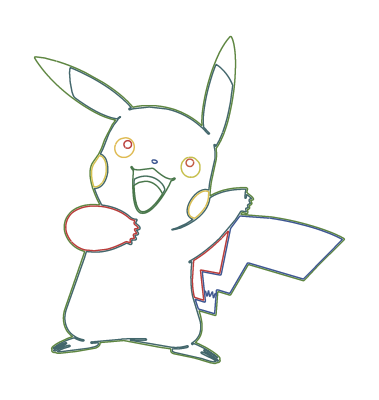

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]], Line[#]}& /@ hLines]
```

```mathematica
Graphics[BSplineCurve[#, SplineDegree -> 6, SplineClosed -> True]& /@ hLines]
```

-Graphics-

```mathematica
(* Fourier coefficients of a single curve *)
fourierComponentData[pointList_, nMax_, op_] := 
Module[{ε=10^-3, μ = 2^14, M = 10000,s,
             scale, Δ, L , nds, sMax, if, 𝓍𝓎Function, X, Y, XFT, YFT,type},
(* prepare curve *)
scale = 1. Mean[Table[ Max[ fl/@ pointList] - Min[fl /@ pointList],{fl,{First, Last}}]];
 Δ=EuclideanDistance[First[pointList], Last[pointList]];
 L=Which[op === "Closed", type="Closed";
                                                        If[First[pointList]===Last[pointList], 
                                                           pointList,Append[pointList, First[pointList]]], 
                op === "Open",type="Open";pointList,
                 Δ==0.,type="Closed";  pointList,
                 Δ/scale<op, type="Closed"; Append[pointList, First[pointList]],
                True,  type="Open"; Join[pointList, Rest[Reverse[pointList]]]];
(* re-parametrize curve by arclength *)
𝓍𝓎Function =BSplineFunction[L, SplineDegree->4];
nds = NDSolve[{s'[t]==Sqrt[𝓍𝓎Function'[t].𝓍𝓎Function'[t]], s[0]==0},s, 
                          {t, 0, 1}, MaxSteps -> 10^5, PrecisionGoal -> 4];
(* total curve length *)
     sMax= s[1]/.nds[[1]];
     if=Interpolation[Table[{s[σ]/.nds[[1]], σ}, {σ,0, 1, 1/M}]];
X[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[1]];
Y[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[2]]; 
(* extract Fourier coefficients *)
{XFT, YFT} = Fourier[Table[#[N @ t], {t, -Pi+ε, Pi - ε, (2Pi-2ε)/μ}]]& /@ {X, Y};   
{type,2Pi/Sqrt[μ] *
((Transpose[Table[{Re[#], Im[#]}&[Exp[I k Pi]  #[[k+1]]], {k, 0, nMax}]]& /@ {XFT, YFT}))}  ]
```

```mathematica
Options[fourierComponents] = {"MaxOrder" -> 180, "OpenClose" -> 0.025};

fourierComponents[pointLists_,OptionsPattern[]] := 
Monitor[Table[fourierComponentData[pointLists[[k]],                           
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["MaxOrder"]],
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["OpenClose"]]],
                         {k, Length[pointLists]}],
Grid[{{Text[Style["progress calculating Fourier coefficients", Darker[Green, 0.66]]], ProgressIndicator[k/Length[pointLists]]} }, 
        Alignment -> Left, Dividers -> Center]]/; Depth[pointLists] === 4
```

```mathematica
fCs = fourierComponents[hLines];
```

```mathematica
sinAmplitudeForm[kt_, {cF_, sF_}] := With[{φ = phase[cF, sF]}, Sqrt[cF^2+sF^2] Sin[kt+ φ]]

phase[cF_, sF_] := With[{T = Sqrt[cF^2+sF^2]},
With[{g = Total[Abs[Table[cF Cos[x] +sF Sin[x]-  T Sin[x+#1 ArcSin[cF/T]+#2],{x, 0, 1, 0.1}]]]&}, 
          If[g[1, 0]<   g[-1, Pi],  ArcSin[cF/T],Pi-ArcSin[cF/T]]]]
```

```mathematica
singleParametrization[fCs_, t_, n_] :=
 UnitStep[Sign[ Sqrt[Sin[t/2]]]] *
 Sum[UnitStep[t-((m -1)4Pi-Pi)]UnitStep[(m -1)4Pi + 3 Pi-t]*
({+fCs[[m,2, 1, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 1, 1, k+1]], fCs[[m,2, 1, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}],   
 +fCs[[m,2, 2, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 2, 1, k+1]], fCs[[m,2, 2, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}]} ),
{m, Length[fCs]}]
```

```mathematica
makeFourierSeries[{"Closed" | "Open", {{cax_, sax_},{cay_, say_}}}, t_, n_] :=
 {Sum[If[k==0, 1/2, 1]cax[[k+1]] Cos[k t]+sax[[k+1]] Sin[k t],{k,0, Min[n, Length[cax]]}],
 Sum[If[k==0, 1/2, 1]cay[[k+1]] Cos[k t]+say[[k+1]] Sin[k t],{k, 0,Min[n, Length[cay]]}]}
```

```mathematica
makeFourierSeriesApproximationManipulate[fCs_, maxOrder_:60] :=
Manipulate[
With[{opts = Sequence[PlotStyle -> Black, Frame -> True, Axes -> False, 
                                         FrameTicks -> None,PlotRange -> All, ImagePadding -> 12]},
Show[{
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Closed", _}]], {t, -Pi, Pi},opts],
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Open", _}]], {t, -Pi, 0},opts]}] // Quiet], 
{{n, 1, "max series order"}, 1, maxOrder,1,Appearance -> "Labeled"},
TrackedSymbols :> True, SaveDefinitions -> True]
```

## Output Section

```mathematica
(* You can change the number of terms in the Fourier decomposition to see how it affects the image. *)
makeFourierSeriesApproximationManipulate[fCs, 180]
```

```mathematica
<<ToMatlab` (* Load ToMatlab *)
```

```mathematica
nTerm = 100; (* Number of terms in your Fourier decompositon, maximum is 180. *)
finalCurve = Rationalize[singleParametrization[fCs, t,nTerm] ,10^-3];
CopyToClipboard[StringReplace[StringReplace[ToMatlab[finalCurve],"UnitStep"->"heaviside"], "Sign"->"sign"]]
```

[(((114221/72)+(-1/619).*sin((40/31)+(-82).*t)+(-1/966).*sin(( ...
  42/29)+(-81).*t)+(-1/538).*sin((28/23)+(-78).*t)+(-1/417).*sin(( ...
  37/25)+(-77).*t)+(-1/506).*sin((79/59)+(-74).*t)+(-1/543).*sin(( ...
  28/27)+(-73).*t)+(-1/776).*sin((39/35)+(-71).*t)+(-1/530).*sin(( ...
  54/43)+(-70).*t)+(-1/620).*sin((67/48)+(-66).*t)+(-1/100).*sin(( ...
  68/47)+(-44).*t)+(-1/89).*sin((37/29)+(-41).*t)+(-2/41).*sin(( ...
  54/37)+(-40).*t)+(-1/42).*sin((43/31)+(-39).*t)+(-1/457).*sin(( ...
  17/16)+(-38).*t)+(-1/50).*sin((49/34)+(-37).*t)+(-1/31).*sin(( ...
  64/47)+(-36).*t)+(-1/20).*sin((67/46)+(-35).*t)+(-1/611).*sin(( ...
  3/25)+(-34).*t)+(-1/48).*sin((51/35)+(-33).*t)+(-1/33).*sin(( ...
  34/25)+(-32).*t)+(-1/26).*sin((51/35)+(-31).*t)+(-1/249).*sin(( ...
  35/33)+(-30).*t)+(-1/16).*sin((42/29)+(-29).*t)+(-4/39).*sin(( ...
  59/40)+(-28).*t)+(-1/28).*sin((13/9)+(-27).*t)+(-3/40).*sin(( ...
  89/59)+(-25).*t)+(-2/25).*sin((323/215)+(-24).*t)+(-2/31).*sin(( ...
  43/28)+(-22).*t)+(-1/101).*sin((43/28)+(-20).*t)+(-1/37).*sin(( ...
  19/13)+(-19).*t)+(-1/32).*sin((43/28)+(-18).*t)+(-3/37).*sin(( ...
  352/235)+(-16).*t)+(-2/23).*sin((57/37)+(-14).*t)+(-1/22).*sin(( ...
  35/24)+(-13).*t)+(-4/25).*sin((50/33)+(-11).*t)+(-7/16).*sin(( ...
  57/37)+(-10).*t)+(-1/19).*sin((66/47)+(-9).*t)+(-1/23).*sin(( ...
  47/32)+(-7).*t)+(-39/22).*sin((53/34)+(-6).*t)+(-785/27).*sin(( ...
  36/23)+(-2).*t)+(-19/27).*sin((17/11)+(-1).*t)+(17/21).*sin(( ...
  71/46)+3.*t)+(8/31).*sin((45/28)+4.*t)+(48/97).*sin((59/38)+5.*t)+ ...
  (7/31).*sin((51/32)+8.*t)+(1/19).*sin((79/46)+12.*t)+(1/158).*sin( ...
  (11/12)+15.*t)+(1/782).*sin((44/17)+17.*t)+(1/107).*sin((52/37)+ ...
  21.*t)+(1/27).*sin((47/30)+23.*t)+(1/32).*sin((14/9)+26.*t)+(1/67) ...
  .*sin((14/9)+42.*t)+(1/197).*sin((151/33)+43.*t)+(1/225).*sin(( ...
  43/30)+45.*t)+(1/122).*sin((9/5)+46.*t)+(1/353).*sin((86/69)+47.* ...
  t)+(1/112).*sin((245/52)+48.*t)+(1/230).*sin((66/37)+49.*t)+( ...
  1/127).*sin((18/11)+50.*t)+(1/363).*sin((143/31)+51.*t)+(1/126).* ...
  sin((91/53)+52.*t)+(1/173).*sin((39/22)+53.*t)+(1/349).*sin(( ...
  81/38)+54.*t)+(1/147).*sin((59/36)+55.*t)+(1/133).*sin((73/43)+ ...
  56.*t)+(1/154).*sin((13/7)+57.*t)+(1/274).*sin((89/51)+58.*t)+( ...
  1/485).*sin((55/36)+60.*t)+(1/247).*sin((53/33)+61.*t)+(1/525).* ...
  sin((56/27)+63.*t)+(1/573).*sin((43/23)+64.*t)+(1/528).*sin(( ...
  91/57)+68.*t)+(1/548).*sin((121/26)+69.*t)).*heaviside(59.*pi+(-1) ...
  .*t).*heaviside((-55).*pi+t)+((32183/16)+(-1/258).*sin((106/85)+( ...
  -98).*t)+(-1/141).*sin((91/61)+(-97).*t)+(-1/373).*sin((15/59)+( ...
  -94).*t)+(-1/407).*sin((36/29)+(-92).*t)+(-1/150).*sin((28/23)+( ...
  -91).*t)+(-1/192).*sin((29/23)+(-87).*t)+(-1/106).*sin((40/33)+( ...
  -83).*t)+(-1/62).*sin((23/20)+(-79).*t)+(-1/128).*sin((23/26)+( ...
  -75).*t)+(-1/78).*sin((26/19)+(-74).*t)+(-1/42).*sin((74/53)+(-72) ...
  .*t)+(-1/91).*sin((4/5)+(-70).*t)+(-1/55).*sin((41/32)+(-68).*t)+( ...
  -1/52).*sin((59/42)+(-66).*t)+(-1/95).*sin((132/131)+(-63).*t)+( ...
  -1/18).*sin((30/23)+(-61).*t)+(-1/25).*sin((73/55)+(-57).*t)+( ...
  -3/35).*sin((211/158)+(-56).*t)+(-1/42).*sin((19/16)+(-52).*t)+( ...
  -2/31).*sin((26/19)+(-49).*t)+(-4/33).*sin((24/17)+(-45).*t)+( ...
  -1/17).*sin((42/29)+(-41).*t)+(-1/41).*sin((45/34)+(-40).*t)+( ...
  -1/48).*sin((60/43)+(-37).*t)+(-1/33).*sin((29/21)+(-36).*t)+( ...
  -1/43).*sin((60/41)+(-30).*t)+(-1/35).*sin((47/36)+(-25).*t)+( ...
  -569/31).*sin((61/39)+(-1).*t)+(1117/28).*sin((30/19)+2.*t)+( ...
  603/58).*sin((68/43)+3.*t)+(7/12).*sin((69/44)+4.*t)+(29/12).*sin( ...
  (51/32)+5.*t)+(13/59).*sin((131/82)+6.*t)+(37/34).*sin((43/27)+7.* ...
  t)+(7/41).*sin((41/26)+8.*t)+(25/34).*sin((8/5)+9.*t)+(1/23).*sin( ...
  (44/25)+10.*t)+(46/77).*sin((55/34)+11.*t)+(2/33).*sin((20/13)+ ...
  12.*t)+(7/19).*sin((35/22)+13.*t)+(1/76).*sin((27/8)+14.*t)+(7/22) ...
  .*sin((34/21)+15.*t)+(4/25).*sin((72/43)+16.*t)+(8/27).*sin(( ...
  50/31)+17.*t)+(2/31).*sin((193/41)+18.*t)+(4/19).*sin((34/21)+19.* ...
  t)+(1/77).*sin((273/62)+20.*t)+(1/8).*sin((21/13)+21.*t)+(2/31).* ...
  sin((22/13)+22.*t)+(1/13).*sin((64/39)+23.*t)+(1/21).*sin((52/29)+ ...
  24.*t)+(2/27).*sin((48/29)+26.*t)+(1/28).*sin((19/11)+27.*t)+( ...
  1/38).*sin((16/9)+28.*t)+(1/101).*sin((370/247)+29.*t)+(1/31).* ...
  sin((134/73)+31.*t)+(1/48).*sin((27/17)+32.*t)+(1/19).*sin((47/28) ...
  +33.*t)+(1/20).*sin((39/23)+34.*t)+(1/44).*sin((73/36)+35.*t)+( ...
  1/12).*sin((48/29)+38.*t)+(1/18).*sin((178/99)+39.*t)+(5/38).*sin( ...
  (77/45)+42.*t)+(1/21).*sin((208/119)+43.*t)+(2/41).*sin((33/20)+ ...
  44.*t)+(3/38).*sin((68/39)+46.*t)+(2/35).*sin((34/19)+47.*t)+( ...
  3/35).*sin((49/29)+48.*t)+(1/49).*sin((47/27)+50.*t)+(1/29).*sin(( ...
  68/35)+51.*t)+(1/43).*sin((83/46)+53.*t)+(1/113).*sin((34/23)+54.* ...
  t)+(1/15).*sin((66/35)+55.*t)+(1/63).*sin((44/21)+58.*t)+(1/34).* ...
  sin((121/69)+59.*t)+(1/28).*sin((49/27)+60.*t)+(1/68).*sin(( ...
  131/30)+62.*t)+(2/39).*sin((11/6)+64.*t)+(1/124).*sin((67/46)+65.* ...
  t)+(1/234).*sin((209/46)+67.*t)+(1/21).*sin((29/16)+69.*t)+(1/31) ...
  .*sin((77/40)+71.*t)+(1/196).*sin((71/46)+73.*t)+(1/62).*sin(( ...
  95/48)+76.*t)+(1/71).*sin((55/32)+77.*t)+(1/294).*sin((256/61)+ ...
  78.*t)+(1/166).*sin((103/40)+80.*t)+(1/83).*sin((50/27)+81.*t)+( ...
  1/280).*sin((25/23)+82.*t)+(1/264).*sin((81/38)+84.*t)+(1/104).* ...
  sin((82/39)+85.*t)+(1/293).*sin((21/23)+86.*t)+(1/104).*sin((13/7) ...
  +88.*t)+(1/723).*sin((112/33)+89.*t)+(1/496).*sin((28/31)+90.*t)+( ...
  1/304).*sin((89/26)+93.*t)+(1/131).*sin((23/13)+95.*t)+(1/729).* ...
  sin((17/4)+96.*t)+(1/107).*sin((77/39)+100.*t)).*heaviside(55.*pi+( ...
  -1).*t).*heaviside((-51).*pi+t)+((66910/53)+(-1/76).*sin((23/17)+( ...
  -71).*t)+(-1/36).*sin((57/41)+(-70).*t)+(-1/92).*sin((45/37)+(-69) ...
  .*t)+(-2/33).*sin((35/27)+(-68).*t)+(-1/77).*sin((38/39)+(-67).*t) ...
  +(-1/75).*sin((251/167)+(-66).*t)+(-1/31).*sin((105/79)+(-65).*t)+ ...
  (-1/88).*sin((36/23)+(-62).*t)+(-1/53).*sin((47/33)+(-50).*t)+( ...
  -1/16).*sin((23/15)+(-48).*t)+(-1/18).*sin((40/27)+(-47).*t)+( ...
  -1243/46).*sin((36/23)+(-2).*t)+(-1405/44).*sin((47/30)+(-1).*t)+( ...
  647/36).*sin((49/31)+3.*t)+(2/17).*sin((285/67)+4.*t)+(22/5).*sin( ...
  (19/12)+5.*t)+(1/18).*sin((217/54)+6.*t)+(45/22).*sin((51/32)+7.* ...
  t)+(2/33).*sin((13/6)+8.*t)+(10/9).*sin((34/21)+9.*t)+(6/37).*sin( ...
  (101/22)+10.*t)+(21/29).*sin((13/8)+11.*t)+(3/25).*sin((169/37)+ ...
  12.*t)+(18/41).*sin((13/8)+13.*t)+(1/51).*sin((84/25)+14.*t)+( ...
  9/50).*sin((53/33)+15.*t)+(2/35).*sin((43/21)+16.*t)+(5/17).*sin(( ...
  59/36)+17.*t)+(2/27).*sin((244/53)+18.*t)+(5/22).*sin((44/27)+19.* ...
  t)+(7/38).*sin((46/27)+20.*t)+(9/38).*sin((117/70)+21.*t)+(1/30).* ...
  sin((179/41)+22.*t)+(11/32).*sin((28/17)+23.*t)+(1/16).*sin(( ...
  45/23)+24.*t)+(1/86).*sin((106/25)+25.*t)+(1/44).*sin((61/23)+26.* ...
  t)+(3/32).*sin((118/71)+27.*t)+(1/48).*sin((148/35)+28.*t)+(5/32) ...
  .*sin((79/46)+29.*t)+(1/29).*sin((36/17)+30.*t)+(4/33).*sin(( ...
  63/37)+31.*t)+(1/29).*sin((29/15)+32.*t)+(3/44).*sin((50/29)+33.* ...
  t)+(1/31).*sin((54/23)+34.*t)+(5/42).*sin((79/46)+35.*t)+(1/45).* ...
  sin((310/73)+36.*t)+(2/21).*sin((26/15)+37.*t)+(2/33).*sin((61/31) ...
  +38.*t)+(3/32).*sin((65/36)+39.*t)+(1/18).*sin((24/13)+40.*t)+( ...
  3/34).*sin((26/15)+41.*t)+(1/19).*sin((41/21)+42.*t)+(1/8).*sin(( ...
  7/4)+43.*t)+(1/50).*sin((99/23)+44.*t)+(2/37).*sin((28/17)+45.*t)+ ...
  (1/36).*sin((79/40)+46.*t)+(1/396).*sin((64/25)+49.*t)+(1/208).* ...
  sin((95/21)+51.*t)+(1/25).*sin((43/22)+52.*t)+(4/39).*sin((37/21)+ ...
  53.*t)+(1/101).*sin((16/7)+54.*t)+(2/27).*sin((121/69)+55.*t)+( ...
  4/45).*sin((15/8)+56.*t)+(1/35).*sin((61/30)+57.*t)+(1/52).*sin(( ...
  9/2)+58.*t)+(1/57).*sin((409/91)+59.*t)+(1/32).*sin((73/37)+60.*t) ...
  +(1/60).*sin((37/17)+61.*t)+(2/31).*sin((79/45)+63.*t)+(1/36).* ...
  sin((25/14)+64.*t)+(1/32).*sin((47/27)+72.*t)+(1/48).*sin((29/16)+ ...
  73.*t)+(1/30).*sin((49/25)+74.*t)+(1/24).*sin((61/32)+75.*t)+( ...
  1/127).*sin((99/28)+76.*t)+(1/28).*sin((53/27)+77.*t)+(1/84).*sin( ...
  (71/26)+78.*t)+(1/79).*sin((28/11)+79.*t)+(1/28).*sin((77/37)+80.* ...
  t)+(1/52).*sin((54/25)+81.*t)+(1/84).*sin((89/34)+82.*t)+(1/22).* ...
  sin((60/31)+83.*t)+(1/110).*sin((96/25)+84.*t)+(1/87).*sin((83/39) ...
  +85.*t)+(1/42).*sin((53/25)+86.*t)+(1/192).*sin((33/14)+87.*t)+( ...
  1/92).*sin((52/23)+88.*t)+(1/44).*sin((137/69)+89.*t)+(1/92).*sin( ...
  (149/64)+90.*t)+(1/48).*sin((43/22)+91.*t)+(1/232).*sin((192/55)+ ...
  92.*t)+(1/64).*sin((107/54)+93.*t)+(1/97).*sin((145/61)+94.*t)+( ...
  1/194).*sin((136/29)+95.*t)+(1/208).*sin((127/38)+96.*t)+(1/55).* ...
  sin((863/432)+97.*t)+(1/182).*sin((133/31)+98.*t)+(1/202).*sin(( ...
  25/12)+99.*t)+(1/115).*sin((61/30)+100.*t)).*heaviside(51.*pi+(-1) ...
  .*t).*heaviside((-47).*pi+t)+((56467/25)+(-1/29).*sin((24/29)+(-98) ...
  .*t)+(-1/22).*sin((25/21)+(-96).*t)+(-2/31).*sin((37/24)+(-86).*t) ...
  +(-1/21).*sin((17/15)+(-84).*t)+(-2/33).*sin((11/30)+(-83).*t)+( ...
  -2/29).*sin((45/134)+(-80).*t)+(-1/16).*sin((4/17)+(-75).*t)+( ...
  -5/51).*sin((22/21)+(-74).*t)+(-2/27).*sin((37/32)+(-72).*t)+( ...
  -4/21).*sin((64/47)+(-67).*t)+(-7/29).*sin((25/18)+(-56).*t)+( ...
  -3/40).*sin((23/25)+(-45).*t)+(-5/19).*sin((61/51)+(-44).*t)+( ...
  -2/31).*sin((71/95)+(-42).*t)+(-5/24).*sin((25/22)+(-41).*t)+( ...
  -3/43).*sin((40/41)+(-40).*t)+(-1/27).*sin((13/46)+(-39).*t)+( ...
  -28/139).*sin((59/42)+(-38).*t)+(-5/49).*sin((27/25)+(-34).*t)+( ...
  -5/24).*sin((40/39)+(-33).*t)+(-7/16).*sin((47/38)+(-32).*t)+( ...
  -4/21).*sin((37/41)+(-31).*t)+(-3/28).*sin((16/17)+(-30).*t)+( ...
  -3/29).*sin((113/94)+(-28).*t)+(-5/17).*sin((47/32)+(-26).*t)+( ...
  -4/35).*sin((55/39)+(-22).*t)+(-1/9).*sin((31/26)+(-21).*t)+(-2/5) ...
  .*sin((10/7)+(-20).*t)+(2018/39).*sin((30/19)+t)+(109/68).*sin(( ...
  43/25)+2.*t)+(161/37).*sin((75/47)+3.*t)+(100/67).*sin((106/23)+ ...
  4.*t)+(103/26).*sin((85/52)+5.*t)+(122/57).*sin((39/23)+6.*t)+( ...
  38/37).*sin((67/39)+7.*t)+(2/3).*sin((181/39)+8.*t)+(3/34).*sin(( ...
  47/21)+9.*t)+(1/14).*sin((155/39)+10.*t)+(2/23).*sin((73/35)+11.* ...
  t)+(16/81).*sin((162/37)+12.*t)+(26/23).*sin((53/32)+13.*t)+( ...
  10/37).*sin((535/119)+14.*t)+(14/51).*sin((21/13)+15.*t)+(5/23).* ...
  sin((137/30)+16.*t)+(6/11).*sin((17/10)+17.*t)+(2/23).*sin((48/23) ...
  +18.*t)+(1/44).*sin((43/42)+19.*t)+(2/31).*sin((49/44)+23.*t)+( ...
  6/41).*sin((136/29)+24.*t)+(32/65).*sin((13/8)+25.*t)+(1/17).*sin( ...
  (7/30)+27.*t)+(4/27).*sin((11/8)+29.*t)+(4/33).*sin((62/41)+35.*t) ...
  +(1/7).*sin((53/27)+36.*t)+(11/28).*sin((17/10)+37.*t)+(2/17).* ...
  sin((41/31)+43.*t)+(12/71).*sin((72/37)+46.*t)+(1/20).*sin((55/26) ...
  +47.*t)+(3/25).*sin((597/128)+48.*t)+(7/29).*sin((64/33)+49.*t)+( ...
  1/16).*sin((72/23)+50.*t)+(1/23).*sin(4+51.*t)+(3/29).*sin(( ...
  112/51)+52.*t)+(2/39).*sin((146/53)+53.*t)+(1/22).*sin((57/14)+ ...
  54.*t)+(1/28).*sin((51/37)+55.*t)+(2/19).*sin((47/25)+57.*t)+( ...
  2/37).*sin((25/9)+58.*t)+(1/35).*sin((49/17)+59.*t)+(1/21).*sin(( ...
  193/69)+60.*t)+(2/41).*sin((48/17)+61.*t)+(2/39).*sin((57/20)+62.* ...
  t)+(1/20).*sin((23/7)+63.*t)+(1/14).*sin((46/21)+64.*t)+(1/20).* ...
  sin((171/46)+65.*t)+(2/27).*sin((45/26)+66.*t)+(1/17).*sin((40/29) ...
  +68.*t)+(3/37).*sin((162/35)+69.*t)+(3/22).*sin((86/45)+70.*t)+( ...
  1/17).*sin((69/38)+71.*t)+(2/25).*sin((32/23)+73.*t)+(1/19).*sin(( ...
  31/33)+76.*t)+(1/26).*sin((5/24)+77.*t)+(2/29).*sin((25/22)+78.*t) ...
  +(1/21).*sin((3/28)+79.*t)+(1/29).*sin((23/25)+81.*t)+(1/30).*sin( ...
  (44/45)+82.*t)+(4/43).*sin((43/23)+85.*t)+(1/49).*sin((97/29)+87.* ...
  t)+(2/23).*sin((67/27)+88.*t)+(1/23).*sin((190/49)+89.*t)+(1/20).* ...
  sin((79/17)+90.*t)+(1/25).*sin((59/20)+91.*t)+(1/26).*sin((123/34) ...
  +92.*t)+(1/59).*sin((83/26)+93.*t)+(1/57).*sin((83/26)+94.*t)+( ...
  1/230).*sin((15/14)+95.*t)+(1/38).*sin((13/12)+97.*t)+(1/52).*sin( ...
  (31/28)+99.*t)+(1/32).*sin((37/25)+100.*t)).*heaviside(47.*pi+(-1) ...
  .*t).*heaviside((-43).*pi+t)+((50651/33)+(-1/64).*sin((49/32)+(-88) ...
  .*t)+(-1/53).*sin((23/38)+(-64).*t)+(-1/96).*sin((2/21)+(-61).*t)+ ...
  (-2/31).*sin((67/45)+(-57).*t)+(-1/38).*sin((10/19)+(-27).*t)+( ...
  -1/11).*sin((52/35)+(-21).*t)+(-2/17).*sin((31/21)+(-20).*t)+( ...
  -74/21).*sin((36/23)+(-7).*t)+(-92/43).*sin((65/44)+(-4).*t)+( ...
  8891/48).*sin((36/23)+t)+(517/36).*sin((47/10)+2.*t)+(77/24).*sin( ...
  (51/31)+3.*t)+(214/61).*sin((144/31)+5.*t)+(17/37).*sin((14/3)+6.* ...
  t)+(5/13).*sin((29/7)+8.*t)+(67/27).*sin((212/45)+9.*t)+(12/25).* ...
  sin((55/12)+10.*t)+(61/42).*sin((200/43)+11.*t)+(31/40).*sin(( ...
  14/3)+12.*t)+(3/4).*sin((285/62)+13.*t)+(19/22).*sin((107/23)+14.* ...
  t)+(4/11).*sin((40/9)+15.*t)+(17/25).*sin((134/29)+16.*t)+(5/41).* ...
  sin((178/39)+17.*t)+(8/21).*sin((113/25)+18.*t)+(1/22).*sin(( ...
  101/33)+19.*t)+(1/31).*sin((361/103)+22.*t)+(2/15).*sin((135/29)+ ...
  23.*t)+(1/10).*sin((7/6)+24.*t)+(1/14).*sin((80/17)+25.*t)+(2/17) ...
  .*sin((18/11)+26.*t)+(1/109).*sin((80/21)+28.*t)+(2/35).*sin(( ...
  63/34)+29.*t)+(3/28).*sin((158/35)+30.*t)+(1/55).*sin((89/29)+31.* ...
  t)+(7/37).*sin((198/43)+32.*t)+(1/32).*sin((56/25)+33.*t)+(3/31).* ...
  sin((191/41)+34.*t)+(1/15).*sin((142/33)+35.*t)+(1/19).*sin(( ...
  287/67)+36.*t)+(2/15).*sin((125/27)+37.*t)+(1/114).*sin((99/28)+ ...
  38.*t)+(3/20).*sin((437/97)+39.*t)+(1/30).*sin((134/51)+40.*t)+( ...
  7/48).*sin((121/26)+41.*t)+(1/25).*sin((64/17)+42.*t)+(3/31).*sin( ...
  (128/29)+43.*t)+(1/23).*sin((84/19)+44.*t)+(1/68).*sin((55/24)+ ...
  45.*t)+(1/24).*sin((125/28)+46.*t)+(2/35).*sin((5/3)+47.*t)+(1/8) ...
  .*sin((134/29)+48.*t)+(1/56).*sin((69/29)+49.*t)+(5/49).*sin(( ...
  185/41)+50.*t)+(1/43).*sin((79/23)+51.*t)+(1/12).*sin((135/29)+ ...
  52.*t)+(1/29).*sin((96/23)+53.*t)+(1/50).*sin((275/69)+54.*t)+( ...
  1/15).*sin((319/72)+55.*t)+(1/22).*sin((84/43)+56.*t)+(1/19).*sin( ...
  (91/53)+58.*t)+(1/17).*sin((91/20)+59.*t)+(1/17).*sin((16/11)+60.* ...
  t)+(1/49).*sin((51/13)+62.*t)+(1/92).*sin((168/47)+63.*t)+(1/19).* ...
  sin((37/26)+65.*t)+(1/29).*sin((89/19)+66.*t)+(1/35).*sin((55/26)+ ...
  67.*t)+(1/16).*sin((136/29)+68.*t)+(1/107).*sin((65/38)+69.*t)+( ...
  1/43).*sin((104/25)+70.*t)+(1/33).*sin((149/150)+71.*t)+(1/30).* ...
  sin((23/17)+72.*t)+(1/130).*sin((14/5)+73.*t)+(1/127).*sin((35/17) ...
  +74.*t)+(1/39).*sin((117/25)+75.*t)+(1/53).*sin((43/26)+76.*t)+( ...
  1/42).*sin((53/12)+77.*t)+(1/110).*sin((89/42)+78.*t)+(1/24).*sin( ...
  (236/51)+79.*t)+(1/623).*sin((31/26)+80.*t)+(1/92).*sin((142/33)+ ...
  81.*t)+(1/54).*sin((31/36)+82.*t)+(1/20).*sin((13/11)+83.*t)+( ...
  1/32).*sin((27/26)+84.*t)+(1/47).*sin((94/93)+85.*t)+(1/62).*sin(( ...
  86/19)+86.*t)+(1/126).*sin((20/13)+87.*t)+(1/161).*sin((71/25)+ ...
  89.*t)+(1/89).*sin((123/32)+90.*t)+(1/58).*sin((41/39)+91.*t)+( ...
  1/686).*sin((86/25)+92.*t)+(1/83).*sin((93/26)+93.*t)+(1/105).* ...
  sin((94/35)+94.*t)+(1/75).*sin((99/25)+95.*t)+(1/33).*sin((14/3)+ ...
  96.*t)+(1/20).*sin((96/23)+97.*t)+(2/39).*sin((204/49)+98.*t)+( ...
  1/22).*sin((205/47)+99.*t)+(1/56).*sin((62/15)+100.*t)).*heaviside( ...
  43.*pi+(-1).*t).*heaviside((-39).*pi+t)+((135380/67)+(-1/39).*sin(( ...
  59/58)+(-96).*t)+(-1/27).*sin((15/61)+(-83).*t)+(-1/54).*sin(( ...
  23/15)+(-82).*t)+(-1/96).*sin((11/10)+(-80).*t)+(-1/50).*sin(( ...
  3/35)+(-79).*t)+(-1/14).*sin((5/18)+(-76).*t)+(-1/37).*sin(( ...
  99/100)+(-72).*t)+(-1/70).*sin((1/3)+(-71).*t)+(-1/41).*sin(( ...
  39/97)+(-69).*t)+(-1/20).*sin((53/38)+(-62).*t)+(-1/241).*sin(( ...
  17/20)+(-56).*t)+(-1/28).*sin((21/74)+(-54).*t)+(-2/19).*sin(( ...
  11/18)+(-53).*t)+(-1/16).*sin((5/38)+(-49).*t)+(-3/44).*sin((4/3)+ ...
  (-46).*t)+(-2/39).*sin((50/37)+(-41).*t)+(-1/35).*sin((25/16)+( ...
  -40).*t)+(-1/11).*sin((8/27)+(-37).*t)+(-1/11).*sin((41/36)+(-34) ...
  .*t)+(-1/22).*sin((33/26)+(-30).*t)+(-3/32).*sin((9/14)+(-19).*t)+ ...
  (-4/19).*sin((48/31)+(-14).*t)+(-4/47).*sin((29/86)+(-11).*t)+( ...
  -11/45).*sin((44/43)+(-9).*t)+(-32/97).*sin((25/28)+(-6).*t)+( ...
  -5/24).*sin((14/11)+(-5).*t)+(3550/31).*sin((59/20)+t)+(22/19).* ...
  sin((41/13)+2.*t)+(42/83).*sin((94/33)+3.*t)+(12/31).*sin((83/29)+ ...
  4.*t)+(10/21).*sin((36/23)+7.*t)+(11/30).*sin((73/24)+8.*t)+(5/37) ...
  .*sin((23/17)+10.*t)+(9/40).*sin((61/23)+12.*t)+(8/41).*sin(( ...
  18/31)+13.*t)+(1/15).*sin((7/22)+15.*t)+(7/48).*sin((76/35)+16.*t) ...
  +(1/33).*sin((118/35)+17.*t)+(2/25).*sin((95/26)+18.*t)+(3/46).* ...
  sin((43/16)+20.*t)+(1/19).*sin((19/27)+21.*t)+(1/40).*sin((98/37)+ ...
  22.*t)+(2/25).*sin((9/16)+23.*t)+(2/33).*sin((104/25)+24.*t)+( ...
  1/13).*sin((65/18)+25.*t)+(1/24).*sin((116/25)+26.*t)+(1/73).*sin( ...
  (28/9)+27.*t)+(3/31).*sin((84/41)+28.*t)+(2/23).*sin((16/79)+29.* ...
  t)+(4/45).*sin((25/18)+31.*t)+(2/25).*sin((79/27)+32.*t)+(1/20).* ...
  sin((75/17)+33.*t)+(1/19).*sin((71/18)+35.*t)+(1/12).*sin((14/19)+ ...
  36.*t)+(3/34).*sin((30/11)+38.*t)+(2/21).*sin((43/20)+39.*t)+( ...
  1/24).*sin((67/24)+42.*t)+(1/17).*sin((29/39)+43.*t)+(1/113).*sin( ...
  (109/27)+44.*t)+(1/20).*sin((74/23)+45.*t)+(1/74).*sin((140/51)+ ...
  47.*t)+(1/15).*sin((54/37)+48.*t)+(1/11).*sin((54/13)+50.*t)+( ...
  3/32).*sin((59/22)+51.*t)+(1/35).*sin((55/56)+52.*t)+(1/18).*sin(( ...
  141/71)+55.*t)+(1/27).*sin((113/30)+57.*t)+(1/48).*sin((45/16)+ ...
  58.*t)+(1/57).*sin((283/66)+59.*t)+(1/30).*sin((422/141)+60.*t)+( ...
  1/28).*sin((5/12)+61.*t)+(1/27).*sin((27/10)+63.*t)+(1/47).*sin(( ...
  11/31)+64.*t)+(1/27).*sin((13/27)+65.*t)+(1/23).*sin((5/19)+66.*t) ...
  +(1/33).*sin((137/34)+67.*t)+(2/29).*sin((82/21)+68.*t)+(1/18).* ...
  sin((20/19)+70.*t)+(1/44).*sin((53/19)+73.*t)+(2/35).*sin((34/13)+ ...
  74.*t)+(1/94).*sin((143/45)+75.*t)+(1/46).*sin((11/23)+77.*t)+( ...
  2/35).*sin((91/31)+78.*t)+(1/179).*sin((60/23)+81.*t)+(1/41).*sin( ...
  (41/27)+84.*t)+(1/30).*sin((53/26)+85.*t)+(1/75).*sin((174/37)+ ...
  86.*t)+(1/97).*sin((8/3)+87.*t)+(1/61).*sin((114/25)+89.*t)+( ...
  1/585).*sin((1/34)+90.*t)+(1/38).*sin((13/21)+91.*t)+(1/101).*sin( ...
  (34/11)+92.*t)+(1/33).*sin((75/32)+93.*t)+(1/93).*sin((111/43)+ ...
  94.*t)+(1/229).*sin((34/15)+95.*t)+(1/37).*sin((128/29)+97.*t)+( ...
  1/56).*sin((30/19)+98.*t)+(1/43).*sin((16/39)+99.*t)+(1/67).*sin(( ...
  79/21)+100.*t)).*heaviside(39.*pi+(-1).*t).*heaviside((-35).*pi+t)+( ...
  (22009/18)+(-1/60).*sin((3/19)+(-99).*t)+(-1/43).*sin((12/13)+( ...
  -98).*t)+(-1/39).*sin((17/28)+(-96).*t)+(-1/152).*sin((13/19)+( ...
  -91).*t)+(-1/60).*sin((69/53)+(-87).*t)+(-1/33).*sin((7/50)+(-85) ...
  .*t)+(-1/42).*sin((18/91)+(-84).*t)+(-1/36).*sin((261/262)+(-79).* ...
  t)+(-1/30).*sin((16/23)+(-78).*t)+(-1/31).*sin((14/39)+(-77).*t)+( ...
  -1/52).*sin((20/43)+(-75).*t)+(-2/33).*sin((27/29)+(-70).*t)+( ...
  -1/22).*sin((1/40)+(-68).*t)+(-2/33).*sin((33/43)+(-60).*t)+( ...
  -1/41).*sin((49/34)+(-52).*t)+(-3/32).*sin((26/33)+(-50).*t)+( ...
  -3/35).*sin((11/27)+(-48).*t)+(-1/37).*sin((9/23)+(-36).*t)+( ...
  -1/25).*sin((11/18)+(-30).*t)+(-2/31).*sin((2/37)+(-27).*t)+( ...
  -1/39).*sin((16/29)+(-25).*t)+(-2/25).*sin((15/37)+(-24).*t)+( ...
  -1/12).*sin((1/44)+(-20).*t)+(-1/13).*sin((62/45)+(-9).*t)+(-3/28) ...
  .*sin((7/8)+(-7).*t)+(-1).*sin((26/19)+(-3).*t)+(3185/27).*sin(( ...
  21/17)+t)+(4/9).*sin((1/3)+2.*t)+(13/31).*sin((5/7)+4.*t)+(2/29).* ...
  sin((117/28)+5.*t)+(2/15).*sin((27/17)+6.*t)+(5/44).*sin((53/14)+ ...
  8.*t)+(2/27).*sin((13/37)+10.*t)+(2/33).*sin((25/6)+11.*t)+(1/52) ...
  .*sin((59/25)+12.*t)+(1/47).*sin((107/33)+13.*t)+(1/22).*sin(( ...
  87/22)+14.*t)+(4/41).*sin((69/35)+15.*t)+(10/69).*sin((53/33)+16.* ...
  t)+(2/17).*sin((19/25)+17.*t)+(2/27).*sin((4/29)+18.*t)+(2/33).* ...
  sin((43/42)+19.*t)+(1/30).*sin((113/45)+21.*t)+(2/17).*sin((11/23) ...
  +22.*t)+(1/19).*sin((56/29)+23.*t)+(4/35).*sin((40/9)+26.*t)+( ...
  2/37).*sin((121/30)+28.*t)+(1/67).*sin((67/133)+29.*t)+(1/28).* ...
  sin((28/25)+31.*t)+(1/31).*sin((151/45)+32.*t)+(1/24).*sin((2/15)+ ...
  33.*t)+(1/41).*sin((16/11)+34.*t)+(2/25).*sin((58/13)+35.*t)+( ...
  3/29).*sin((107/30)+37.*t)+(1/14).*sin((171/46)+38.*t)+(4/43).* ...
  sin((63/23)+39.*t)+(3/34).*sin((139/50)+40.*t)+(1/30).*sin((31/12) ...
  +41.*t)+(1/13).*sin((86/41)+42.*t)+(1/364).*sin((44/27)+43.*t)+( ...
  1/15).*sin((37/30)+44.*t)+(1/21).*sin((117/44)+45.*t)+(1/34).*sin( ...
  (26/35)+46.*t)+(3/43).*sin((46/33)+47.*t)+(1/44).*sin((11/35)+49.* ...
  t)+(1/18).*sin((62/25)+51.*t)+(1/11).*sin((47/30)+53.*t)+(1/33).* ...
  sin((21/22)+54.*t)+(1/20).*sin((20/19)+55.*t)+(1/27).*sin((11/18)+ ...
  56.*t)+(1/66).*sin((35/22)+57.*t)+(1/81).*sin((14/25)+58.*t)+( ...
  1/75).*sin((103/36)+59.*t)+(1/35).*sin((22/23)+61.*t)+(4/45).*sin( ...
  (110/27)+62.*t)+(1/27).*sin((19/21)+63.*t)+(2/23).*sin((25/8)+64.* ...
  t)+(1/42).*sin((15/32)+65.*t)+(1/19).*sin((59/23)+66.*t)+(1/57).* ...
  sin((1/47)+67.*t)+(1/46).*sin((35/43)+69.*t)+(1/28).*sin((16/23)+ ...
  71.*t)+(1/90).*sin((55/16)+72.*t)+(1/23).*sin((13/23)+73.*t)+( ...
  1/21).*sin((40/27)+74.*t)+(1/19).*sin((11/41)+76.*t)+(1/73).*sin(( ...
  123/40)+80.*t)+(1/70).*sin((123/43)+81.*t)+(1/31).*sin((144/53)+ ...
  82.*t)+(1/81).*sin((14/15)+83.*t)+(1/22).*sin((202/43)+86.*t)+( ...
  1/27).*sin((506/119)+88.*t)+(1/94).*sin((33/10)+89.*t)+(1/29).* ...
  sin((131/29)+90.*t)+(1/70).*sin((31/8)+92.*t)+(1/323).*sin((51/29) ...
  +93.*t)+(1/120).*sin((1/70)+94.*t)+(1/100).*sin((31/18)+95.*t)+( ...
  1/64).*sin((17/18)+97.*t)+(1/296).*sin((21/38)+100.*t)).*heaviside( ...
  35.*pi+(-1).*t).*heaviside((-31).*pi+t)+((50869/24)+(-1/69).*sin(( ...
  1/5)+(-94).*t)+(-1/88).*sin((49/40)+(-92).*t)+(-1/28).*sin((2/33)+ ...
  (-91).*t)+(-1/24).*sin((12/13)+(-80).*t)+(-1/24).*sin((30/29)+( ...
  -66).*t)+(-1/24).*sin((63/62)+(-58).*t)+(-2/31).*sin((19/51)+(-57) ...
  .*t)+(-1/12).*sin((11/40)+(-55).*t)+(-1/50).*sin((6/13)+(-53).*t)+ ...
  (-2/25).*sin((21/26)+(-50).*t)+(-1/9).*sin((7/30)+(-45).*t)+( ...
  -1/25).*sin((21/40)+(-38).*t)+(-1/13).*sin((64/41)+(-37).*t)+( ...
  -1/83).*sin((3/20)+(-30).*t)+(-3/40).*sin((7/12)+(-29).*t)+(-1/35) ...
  .*sin((102/73)+(-22).*t)+(-1/8).*sin((20/23)+(-18).*t)+(-7/26).* ...
  sin((23/19)+(-15).*t)+(-11/35).*sin((77/58)+(-12).*t)+(-6/11).* ...
  sin((12/31)+(-8).*t)+(-58/21).*sin((51/35)+(-5).*t)+(-157/34).* ...
  sin((26/21)+(-2).*t)+(-2014/17).*sin((39/46)+(-1).*t)+(343/41).* ...
  sin((147/74)+3.*t)+(9/5).*sin((19/15)+4.*t)+(17/26).*sin((123/32)+ ...
  6.*t)+(19/14).*sin((46/29)+7.*t)+(33/46).*sin((47/11)+9.*t)+( ...
  18/31).*sin((127/63)+10.*t)+(7/24).*sin((23/37)+11.*t)+(4/13).* ...
  sin((63/23)+13.*t)+(5/19).*sin((14/13)+14.*t)+(12/61).*sin(( ...
  1163/291)+16.*t)+(9/55).*sin((39/25)+17.*t)+(3/19).*sin((545/136)+ ...
  19.*t)+(3/34).*sin((47/32)+20.*t)+(1/31).*sin((124/29)+21.*t)+( ...
  1/35).*sin((129/29)+23.*t)+(2/21).*sin((29/32)+24.*t)+(2/19).*sin( ...
  (41/26)+25.*t)+(1/60).*sin((40/9)+26.*t)+(1/10).*sin((13/4)+27.*t) ...
  +(1/31).*sin((40/37)+28.*t)+(1/15).*sin((26/23)+31.*t)+(5/36).* ...
  sin((14/17)+32.*t)+(1/61).*sin((61/15)+33.*t)+(2/31).*sin((63/26)+ ...
  34.*t)+(1/14).*sin((73/25)+35.*t)+(1/17).*sin((137/33)+36.*t)+( ...
  7/40).*sin((53/88)+39.*t)+(1/20).*sin((85/26)+40.*t)+(4/29).*sin(( ...
  97/46)+41.*t)+(1/58).*sin((23/47)+42.*t)+(1/9).*sin((56/13)+43.*t) ...
  +(1/23).*sin((16/11)+44.*t)+(4/49).*sin((25/37)+46.*t)+(4/41).* ...
  sin((8/5)+47.*t)+(3/40).*sin((14/15)+48.*t)+(1/12).*sin((19/8)+ ...
  49.*t)+(1/24).*sin((283/66)+51.*t)+(3/35).*sin((1/178)+52.*t)+( ...
  2/35).*sin((87/37)+54.*t)+(2/43).*sin((119/27)+56.*t)+(1/56).*sin( ...
  (29/11)+59.*t)+(1/31).*sin((29/19)+60.*t)+(2/39).*sin((105/26)+ ...
  61.*t)+(1/50).*sin((37/14)+62.*t)+(1/43).*sin((71/32)+63.*t)+( ...
  1/32).*sin((23/5)+64.*t)+(2/37).*sin((59/15)+65.*t)+(1/42).*sin(( ...
  7/10)+67.*t)+(1/14).*sin((11/49)+68.*t)+(3/28).*sin((7/4)+69.*t)+( ...
  1/19).*sin((27/20)+70.*t)+(3/29).*sin((72/25)+71.*t)+(1/45).*sin(( ...
  31/7)+72.*t)+(1/67).*sin((91/25)+73.*t)+(1/30).*sin((37/8)+74.*t)+ ...
  (1/61).*sin((13/48)+75.*t)+(1/34).*sin((139/31)+76.*t)+(1/18).* ...
  sin((8/19)+77.*t)+(1/31).*sin((109/26)+78.*t)+(2/33).*sin((19/27)+ ...
  79.*t)+(1/38).*sin((46/27)+81.*t)+(2/35).*sin((22/19)+82.*t)+( ...
  1/42).*sin((60/31)+83.*t)+(1/20).*sin((94/35)+84.*t)+(1/197).*sin( ...
  (276/65)+85.*t)+(1/74).*sin((78/19)+86.*t)+(1/44).*sin((30/41)+ ...
  87.*t)+(1/26).*sin((79/28)+88.*t)+(1/49).*sin((4/9)+89.*t)+(1/31) ...
  .*sin((145/38)+90.*t)+(1/42).*sin((38/35)+93.*t)+(1/64).*sin(( ...
  103/33)+95.*t)+(2/37).*sin((3/38)+96.*t)+(1/55).*sin((68/23)+97.* ...
  t)+(1/18).*sin((19/23)+98.*t)+(1/42).*sin((51/13)+99.*t)+(1/25).* ...
  sin((88/41)+100.*t)).*heaviside(31.*pi+(-1).*t).*heaviside((-27).* ...
  pi+t)+((13697/15)+(-1/24).*sin((3/11)+(-100).*t)+(-1/69).*sin(( ...
  36/37)+(-99).*t)+(-1/74).*sin((21/17)+(-89).*t)+(-1/24).*sin(( ...
  19/32)+(-85).*t)+(-1/50).*sin((7/24)+(-83).*t)+(-1/15).*sin(( ...
  14/13)+(-82).*t)+(-1/16).*sin((7/57)+(-81).*t)+(-6/53).*sin(( ...
  18/13)+(-80).*t)+(-3/26).*sin((17/31)+(-76).*t)+(-3/44).*sin(( ...
  44/39)+(-73).*t)+(-1/26).*sin((32/23)+(-70).*t)+(-1/23).*sin(( ...
  22/19)+(-63).*t)+(-3/23).*sin((7/17)+(-58).*t)+(-3/38).*sin(( ...
  14/11)+(-50).*t)+(-2/15).*sin((75/56)+(-45).*t)+(-3/35).*sin(( ...
  4/17)+(-44).*t)+(-4/35).*sin((83/124)+(-36).*t)+(-1/23).*sin(( ...
  27/37)+(-34).*t)+(-2/31).*sin((18/23)+(-28).*t)+(-6/61).*sin(( ...
  11/8)+(-22).*t)+(-1/13).*sin((1/24)+(-19).*t)+(-13/40).*sin(( ...
  19/30)+(-14).*t)+(-19/37).*sin((5/27)+(-13).*t)+(-5/14).*sin(( ...
  58/45)+(-11).*t)+(-2/27).*sin((33/31)+(-8).*t)+(-133/23).*sin(( ...
  53/35)+(-3).*t)+(2/15).*sin(27.*t)+(2341/25).*sin((139/39)+t)+( ...
  60/31).*sin((16/79)+2.*t)+(73/30).*sin((65/38)+4.*t)+(71/29).*sin( ...
  (6/13)+5.*t)+(25/27).*sin((113/41)+6.*t)+(37/30).*sin((92/55)+7.* ...
  t)+(17/23).*sin((17/5)+9.*t)+(4/19).*sin((17/7)+10.*t)+(9/40).* ...
  sin((10/3)+12.*t)+(9/46).*sin((77/37)+15.*t)+(5/32).*sin((9/40)+ ...
  16.*t)+(1/19).*sin((26/27)+17.*t)+(3/16).*sin((81/34)+18.*t)+(2/9) ...
  .*sin((73/20)+20.*t)+(2/33).*sin((20/11)+21.*t)+(2/35).*sin(( ...
  79/21)+23.*t)+(1/26).*sin((87/26)+24.*t)+(3/31).*sin((1/37)+25.*t) ...
  +(2/23).*sin((80/29)+26.*t)+(2/19).*sin((89/36)+29.*t)+(2/29).* ...
  sin((41/17)+30.*t)+(1/85).*sin((131/57)+31.*t)+(1/38).*sin((17/32) ...
  +32.*t)+(1/35).*sin((9/10)+33.*t)+(1/69).*sin((23/29)+35.*t)+( ...
  1/11).*sin((260/63)+37.*t)+(3/29).*sin((59/16)+38.*t)+(3/37).*sin( ...
  (35/24)+39.*t)+(3/25).*sin((13/8)+40.*t)+(1/27).*sin((98/39)+41.* ...
  t)+(2/27).*sin((72/19)+42.*t)+(1/15).*sin((33/35)+43.*t)+(1/21).* ...
  sin((77/20)+46.*t)+(1/79).*sin((46/35)+47.*t)+(3/26).*sin((16/13)+ ...
  48.*t)+(2/25).*sin((60/17)+49.*t)+(3/29).*sin((67/43)+51.*t)+( ...
  1/17).*sin((40/37)+52.*t)+(3/38).*sin((123/29)+53.*t)+(1/13).*sin( ...
  (41/14)+54.*t)+(1/112).*sin((42/85)+55.*t)+(3/43).*sin((11/25)+ ...
  56.*t)+(3/29).*sin((145/42)+57.*t)+(3/35).*sin((5/31)+59.*t)+( ...
  1/31).*sin((151/37)+60.*t)+(1/29).*sin((83/23)+61.*t)+(1/29).*sin( ...
  (107/33)+62.*t)+(1/16).*sin((36/23)+64.*t)+(5/39).*sin((27/11)+ ...
  65.*t)+(1/26).*sin((13/22)+66.*t)+(1/57).*sin((78/17)+67.*t)+( ...
  1/28).*sin((104/25)+68.*t)+(1/20).*sin((59/74)+69.*t)+(1/18).*sin( ...
  (153/40)+71.*t)+(3/40).*sin((39/79)+72.*t)+(1/21).*sin((57/28)+ ...
  74.*t)+(1/49).*sin((8/19)+75.*t)+(1/35).*sin((55/12)+77.*t)+(1/18) ...
  .*sin((8/23)+78.*t)+(1/40).*sin((1/193)+79.*t)+(1/26).*sin((20/23) ...
  +84.*t)+(1/32).*sin((77/45)+86.*t)+(1/25).*sin((18/13)+87.*t)+( ...
  2/39).*sin((10/23)+88.*t)+(1/22).*sin((156/37)+90.*t)+(1/44).*sin( ...
  (151/37)+91.*t)+(1/49).*sin((97/23)+92.*t)+(1/41).*sin((115/38)+ ...
  93.*t)+(1/14).*sin((231/71)+94.*t)+(1/172).*sin((77/47)+95.*t)+( ...
  1/25).*sin((37/35)+96.*t)+(1/39).*sin((20/41)+97.*t)+(1/54).*sin(( ...
  31/29)+98.*t)).*heaviside(27.*pi+(-1).*t).*heaviside((-23).*pi+t)+(( ...
  29082/13)+(-1/95).*sin((17/22)+(-100).*t)+(-1/27).*sin((6/43)+( ...
  -89).*t)+(-1/10).*sin((5/37)+(-87).*t)+(-1/65).*sin((13/32)+(-84) ...
  .*t)+(-1/38).*sin((4/11)+(-83).*t)+(-1/17).*sin((1/20)+(-73).*t)+( ...
  -3/37).*sin((18/37)+(-66).*t)+(-2/37).*sin((22/21)+(-64).*t)+( ...
  -1/30).*sin((49/74)+(-63).*t)+(-1/25).*sin((21/20)+(-55).*t)+( ...
  -1/14).*sin((31/20)+(-53).*t)+(-1/4).*sin((3/28)+(-49).*t)+(-1/85) ...
  .*sin((19/32)+(-47).*t)+(-5/29).*sin((61/71)+(-46).*t)+(-5/32).* ...
  sin((1/147)+(-45).*t)+(-4/33).*sin((11/29)+(-39).*t)+(-5/38).*sin( ...
  (38/41)+(-37).*t)+(-5/36).*sin((9/55)+(-31).*t)+(-14/31).*sin(( ...
  59/43)+(-30).*t)+(-6/23).*sin((7/18)+(-29).*t)+(-10/37).*sin(( ...
  11/8)+(-28).*t)+(-7/26).*sin((22/23)+(-27).*t)+(-19/35).*sin(( ...
  15/23)+(-26).*t)+(-3/23).*sin((7/50)+(-20).*t)+(-13/28).*sin(( ...
  7/20)+(-19).*t)+(-103/40).*sin((11/20)+(-9).*t)+(-133/30).*sin(( ...
  31/29)+(-8).*t)+(-13/3).*sin((1/59)+(-6).*t)+(4557/23).*sin(( ...
  165/43)+t)+(651/13).*sin((17/22)+2.*t)+(529/27).*sin((1/16)+3.*t)+ ...
  (947/42).*sin((21/22)+4.*t)+(659/45).*sin((58/35)+5.*t)+(42/11).* ...
  sin((115/26)+7.*t)+(163/36).*sin((499/107)+10.*t)+(49/32).*sin(( ...
  124/29)+11.*t)+(29/32).*sin((628/145)+12.*t)+(7/8).*sin((28/37)+ ...
  13.*t)+(54/25).*sin((50/19)+14.*t)+(47/37).*sin((44/19)+15.*t)+( ...
  15/17).*sin((125/43)+16.*t)+(15/23).*sin((167/36)+17.*t)+(13/22).* ...
  sin((73/37)+18.*t)+(9/44).*sin((453/97)+21.*t)+(28/33).*sin(( ...
  20/19)+22.*t)+(11/26).*sin((58/35)+23.*t)+(14/37).*sin((60/31)+ ...
  24.*t)+(3/19).*sin((152/71)+25.*t)+(7/26).*sin((86/31)+32.*t)+( ...
  4/23).*sin((405/152)+33.*t)+(1/2).*sin((69/22)+34.*t)+(1/33).*sin( ...
  (70/33)+35.*t)+(1/24).*sin((39/35)+36.*t)+(4/39).*sin((97/39)+38.* ...
  t)+(4/19).*sin((31/24)+40.*t)+(7/55).*sin((25/21)+41.*t)+(3/20).* ...
  sin((56/29)+42.*t)+(6/47).*sin((103/30)+43.*t)+(1/17).*sin(( ...
  136/43)+44.*t)+(2/41).*sin((2/25)+48.*t)+(3/19).*sin((183/41)+50.* ...
  t)+(4/27).*sin((85/27)+51.*t)+(5/24).*sin((109/40)+52.*t)+(2/37).* ...
  sin((49/13)+54.*t)+(1/16).*sin((25/24)+56.*t)+(1/40).*sin((125/27) ...
  +57.*t)+(6/47).*sin((37/24)+58.*t)+(1/10).*sin((27/40)+59.*t)+( ...
  1/25).*sin((34/27)+60.*t)+(5/38).*sin((237/74)+61.*t)+(1/24).*sin( ...
  (174/47)+62.*t)+(1/13).*sin((18/13)+65.*t)+(1/31).*sin((54/107)+ ...
  67.*t)+(1/55).*sin((143/31)+68.*t)+(1/35).*sin((69/53)+69.*t)+( ...
  5/51).*sin((154/39)+70.*t)+(3/26).*sin((96/23)+71.*t)+(1/17).*sin( ...
  (117/35)+72.*t)+(3/34).*sin((31/40)+74.*t)+(4/31).*sin((12/31)+ ...
  75.*t)+(5/29).*sin((15/28)+76.*t)+(8/57).*sin((17/24)+77.*t)+( ...
  3/17).*sin((43/29)+78.*t)+(9/50).*sin((45/29)+79.*t)+(4/37).*sin(( ...
  17/14)+80.*t)+(3/35).*sin((9/5)+81.*t)+(1/18).*sin((19/30)+82.*t)+ ...
  (1/23).*sin((54/55)+85.*t)+(3/28).*sin((8/49)+86.*t)+(1/77).*sin(( ...
  155/36)+88.*t)+(1/22).*sin((93/20)+90.*t)+(3/29).*sin((71/17)+91.* ...
  t)+(2/19).*sin((70/27)+92.*t)+(1/23).*sin((44/23)+93.*t)+(1/14).* ...
  sin((3/14)+94.*t)+(2/27).*sin((31/7)+95.*t)+(1/35).*sin((29/15)+ ...
  96.*t)+(1/24).*sin((97/31)+97.*t)+(1/20).*sin((69/31)+98.*t)+( ...
  1/23).*sin((103/30)+99.*t)).*heaviside(23.*pi+(-1).*t).*heaviside(( ...
  -19).*pi+t)+((36129/38)+(-1/25).*sin((29/26)+(-98).*t)+(-1/47).* ...
  sin((43/85)+(-95).*t)+(-1/32).*sin((12/31)+(-89).*t)+(-1/18).*sin( ...
  (7/37)+(-84).*t)+(-4/33).*sin((11/27)+(-83).*t)+(-1/11).*sin(( ...
  25/29)+(-77).*t)+(-1/17).*sin((18/19)+(-76).*t)+(-3/29).*sin(( ...
  11/21)+(-67).*t)+(-8/65).*sin((17/19)+(-66).*t)+(-5/51).*sin(( ...
  31/26)+(-65).*t)+(-4/21).*sin((16/21)+(-55).*t)+(-4/25).*sin(( ...
  26/41)+(-49).*t)+(-7/37).*sin((29/23)+(-48).*t)+(-7/43).*sin(( ...
  13/9)+(-44).*t)+(-26/33).*sin((3/16)+(-27).*t)+(-37/35).*sin(( ...
  51/37)+(-26).*t)+(-10/11).*sin((2/29)+(-14).*t)+(-8/13).*sin(( ...
  15/26)+(-13).*t)+(-235/26).*sin((10/33)+(-2).*t)+(12848/31).*sin(( ...
  68/33)+t)+(197/16).*sin((877/292)+3.*t)+(55/18).*sin((37/23)+4.*t) ...
  +(89/45).*sin((59/35)+5.*t)+(202/67).*sin((12/5)+6.*t)+(46/25).* ...
  sin((77/26)+7.*t)+(37/30).*sin((113/33)+8.*t)+(7/17).*sin((157/34) ...
  +9.*t)+(5/28).*sin((79/34)+10.*t)+(8/57).*sin((36/11)+11.*t)+( ...
  11/23).*sin((256/61)+12.*t)+(21/16).*sin((8/23)+15.*t)+(27/23).* ...
  sin((18/17)+16.*t)+(16/13).*sin((35/31)+17.*t)+(37/38).*sin(( ...
  15/13)+18.*t)+(70/51).*sin((29/24)+19.*t)+(27/14).*sin((60/41)+ ...
  20.*t)+(107/49).*sin((75/41)+21.*t)+(94/39).*sin((29/12)+22.*t)+( ...
  81/34).*sin((38/13)+23.*t)+(27/13).*sin((113/32)+24.*t)+(68/43).* ...
  sin((93/22)+25.*t)+(29/51).*sin((26/29)+28.*t)+(7/13).*sin((52/29) ...
  +29.*t)+(18/29).*sin((85/33)+30.*t)+(11/31).*sin((64/19)+31.*t)+( ...
  8/23).*sin((103/27)+32.*t)+(1/23).*sin((39/16)+33.*t)+(5/41).*sin( ...
  (58/25)+34.*t)+(1/5).*sin((26/9)+35.*t)+(14/55).*sin((80/27)+36.* ...
  t)+(7/46).*sin((85/22)+37.*t)+(8/39).*sin((422/115)+38.*t)+(1/9).* ...
  sin((98/33)+39.*t)+(5/22).*sin((56/17)+40.*t)+(7/25).*sin((85/23)+ ...
  41.*t)+(6/23).*sin((133/33)+42.*t)+(7/30).*sin((119/26)+43.*t)+( ...
  3/34).*sin((290/63)+45.*t)+(5/44).*sin((89/21)+46.*t)+(2/11).*sin( ...
  (194/43)+47.*t)+(3/35).*sin((6/13)+50.*t)+(1/47).*sin((29/16)+51.* ...
  t)+(2/19).*sin((19/6)+52.*t)+(5/31).*sin((93/22)+53.*t)+(2/15).* ...
  sin((59/13)+54.*t)+(1/14).*sin((10/29)+56.*t)+(2/23).*sin((34/69)+ ...
  57.*t)+(1/19).*sin((29/13)+58.*t)+(1/18).*sin((5/2)+59.*t)+(1/12) ...
  .*sin((162/47)+60.*t)+(1/23).*sin((235/59)+61.*t)+(1/13).*sin(( ...
  143/37)+62.*t)+(2/23).*sin((49/11)+63.*t)+(4/29).*sin((236/51)+ ...
  64.*t)+(3/34).*sin((14/47)+68.*t)+(2/17).*sin((8/35)+69.*t)+(1/18) ...
  .*sin((6/7)+70.*t)+(7/62).*sin((36/41)+71.*t)+(1/187).*sin(( ...
  100/53)+72.*t)+(2/29).*sin((57/26)+73.*t)+(1/25).*sin((226/55)+ ...
  74.*t)+(3/37).*sin((138/37)+75.*t)+(5/46).*sin((14/39)+78.*t)+( ...
  1/28).*sin((10/17)+79.*t)+(2/27).*sin((44/21)+80.*t)+(3/38).*sin(( ...
  196/43)+81.*t)+(3/46).*sin((221/55)+82.*t)+(2/21).*sin((55/69)+ ...
  85.*t)+(1/30).*sin((46/51)+86.*t)+(1/36).*sin((25/14)+87.*t)+( ...
  1/30).*sin((4/11)+88.*t)+(3/41).*sin((40/31)+90.*t)+(1/30).*sin(( ...
  25/34)+91.*t)+(1/25).*sin((67/30)+92.*t)+(1/40).*sin((63/20)+94.* ...
  t)+(1/22).*sin((108/35)+96.*t)+(1/361).*sin((26/17)+97.*t)+(1/37) ...
  .*sin((12/37)+99.*t)+(2/29).*sin((3/5)+100.*t)).*heaviside(19.*pi+( ...
  -1).*t).*heaviside((-15).*pi+t)+((51315/34)+(-6/41).*sin((53/46)+( ...
  -89).*t)+(-2/33).*sin((11/23)+(-83).*t)+(-10/27).*sin((40/29)+( ...
  -79).*t)+(-7/32).*sin((19/16)+(-78).*t)+(-37/86).*sin((36/29)+( ...
  -77).*t)+(-4/41).*sin((71/53)+(-67).*t)+(-7/22).*sin((43/31)+(-66) ...
  .*t)+(-2/11).*sin((7/25)+(-65).*t)+(-19/35).*sin((17/11)+(-57).*t) ...
  +(-18/31).*sin((32/25)+(-56).*t)+(-4/7).*sin((23/15)+(-54).*t)+( ...
  -9/37).*sin((4/15)+(-53).*t)+(-2/31).*sin((9/22)+(-52).*t)+( ...
  -41/36).*sin((87/56)+(-51).*t)+(-17/23).*sin((29/19)+(-45).*t)+( ...
  -9/13).*sin((55/41)+(-44).*t)+(-11/13).*sin((60/43)+(-42).*t)+( ...
  -32/43).*sin((60/43)+(-41).*t)+(-11/38).*sin((24/19)+(-40).*t)+( ...
  -13/21).*sin((43/31)+(-32).*t)+(-7/17).*sin((44/31)+(-31).*t)+( ...
  -1/8).*sin((46/41)+(-28).*t)+(-461/154).*sin((35/24)+(-20).*t)+( ...
  -417/71).*sin((49/32)+(-19).*t)+(-157/40).*sin((25/16)+(-17).*t)+( ...
  -157/24).*sin((24/19)+(-8).*t)+(-651/16).*sin((48/31)+(-7).*t)+( ...
  -505/23).*sin((7/5)+(-6).*t)+(-2604/23).*sin((14/9)+(-5).*t)+( ...
  -1365/31).*sin((53/34)+(-4).*t)+(247/15).*sin((55/36)+t)+(2276/27) ...
  .*sin((136/29)+2.*t)+(4519/30).*sin((95/61)+3.*t)+(111/41).*sin(( ...
  35/24)+9.*t)+(5/8).*sin((167/38)+10.*t)+(21/23).*sin((13/10)+11.* ...
  t)+(274/73).*sin((17/10)+12.*t)+(56/29).*sin((18/13)+13.*t)+( ...
  267/22).*sin((164/35)+14.*t)+(83/44).*sin((34/27)+15.*t)+(49/24).* ...
  sin((58/39)+16.*t)+(72/23).*sin((25/19)+18.*t)+(36/29).*sin(( ...
  31/18)+21.*t)+(123/32).*sin((5/3)+22.*t)+(19/39).*sin((121/38)+ ...
  23.*t)+(67/36).*sin((31/18)+24.*t)+(43/28).*sin((11/7)+25.*t)+( ...
  81/29).*sin((188/41)+26.*t)+(318/127).*sin((19/13)+27.*t)+(27/29) ...
  .*sin((172/37)+29.*t)+(7/31).*sin((35/47)+30.*t)+(23/33).*sin(( ...
  179/39)+33.*t)+(19/8).*sin((39/25)+34.*t)+(39/38).*sin((107/24)+ ...
  35.*t)+(55/56).*sin((86/49)+36.*t)+(89/90).*sin((28/17)+37.*t)+( ...
  13/15).*sin((85/19)+38.*t)+(15/61).*sin((25/43)+39.*t)+(57/58).* ...
  sin((25/18)+43.*t)+(13/24).*sin((47/36)+46.*t)+(20/31).*sin((40/9) ...
  +47.*t)+(3/4).*sin((62/35)+48.*t)+(23/42).*sin((33/19)+49.*t)+( ...
  21/64).*sin((128/69)+50.*t)+(35/47).*sin((35/26)+55.*t)+(7/30).* ...
  sin((42/43)+58.*t)+(15/38).*sin((180/103)+59.*t)+(4/23).*sin(( ...
  79/30)+60.*t)+(7/38).*sin((43/23)+61.*t)+(19/56).*sin((242/161)+ ...
  62.*t)+(28/37).*sin((108/23)+63.*t)+(16/45).*sin((39/28)+64.*t)+( ...
  1/14).*sin((53/38)+68.*t)+(3/29).*sin((129/65)+69.*t)+(2/19).*sin( ...
  (123/29)+70.*t)+(15/32).*sin((41/26)+71.*t)+(23/57).*sin((121/27)+ ...
  72.*t)+(2/15).*sin((68/31)+73.*t)+(3/8).*sin((37/24)+74.*t)+(1/11) ...
  .*sin((127/35)+75.*t)+(1/10).*sin((15/16)+76.*t)+(13/28).*sin(( ...
  29/19)+80.*t)+(1/57).*sin((141/49)+81.*t)+(2/13).*sin((64/15)+82.* ...
  t)+(5/22).*sin((716/159)+84.*t)+(3/11).*sin((68/37)+85.*t)+(7/30) ...
  .*sin((79/44)+86.*t)+(1/16).*sin((69/52)+87.*t)+(12/49).*sin(( ...
  146/31)+88.*t)+(1/10).*sin((11/27)+90.*t)+(2/13).*sin((174/37)+ ...
  91.*t)+(1/4).*sin((65/51)+92.*t)+(3/19).*sin((97/22)+93.*t)+(3/35) ...
  .*sin((95/24)+94.*t)+(3/31).*sin((57/28)+95.*t)+(1/15).*sin(( ...
  41/20)+96.*t)+(2/31).*sin((27/13)+97.*t)+(2/25).*sin((42/11)+98.* ...
  t)+(4/45).*sin((15/23)+99.*t)+(7/33).*sin((113/24)+100.*t)).* ...
  heaviside(15.*pi+(-1).*t).*heaviside((-11).*pi+t)+((65032/23)+( ...
  -6/47).*sin((43/30)+(-99).*t)+(-3/28).*sin((3/32)+(-98).*t)+( ...
  -1/12).*sin((25/17)+(-94).*t)+(-2/29).*sin((81/58)+(-93).*t)+( ...
  -2/19).*sin((8/13)+(-83).*t)+(-3/17).*sin((5/11)+(-82).*t)+(-4/23) ...
  .*sin((21/26)+(-79).*t)+(-4/29).*sin((11/13)+(-78).*t)+(-2/17).* ...
  sin((47/40)+(-72).*t)+(-4/31).*sin((35/33)+(-67).*t)+(-4/27).*sin( ...
  (37/38)+(-66).*t)+(-20/53).*sin((1/28)+(-55).*t)+(-1/12).*sin(( ...
  19/24)+(-51).*t)+(-9/16).*sin((7/8)+(-42).*t)+(-21/38).*sin(( ...
  19/66)+(-39).*t)+(-19/30).*sin((23/17)+(-36).*t)+(-35/27).*sin(( ...
  49/44)+(-35).*t)+(-13/9).*sin((3/4)+(-24).*t)+(-64/33).*sin(( ...
  22/27)+(-23).*t)+(-115/36).*sin((5/33)+(-18).*t)+(-25/12).*sin(( ...
  10/19)+(-17).*t)+(-247/79).*sin((7/10)+(-14).*t)+(-239/36).*sin(( ...
  3/11)+(-12).*t)+(-646/29).*sin((13/12)+(-5).*t)+(-232/33).*sin(( ...
  12/37)+(-4).*t)+(-6939/55).*sin((9/11)+(-2).*t)+(10399/14).*sin(( ...
  116/33)+t)+(3061/47).*sin((41/26)+3.*t)+(553/26).*sin((85/54)+6.* ...
  t)+(179/21).*sin((64/15)+7.*t)+(431/35).*sin((85/21)+8.*t)+( ...
  529/30).*sin((66/31)+9.*t)+(951/56).*sin((35/18)+10.*t)+(259/22).* ...
  sin((35/88)+11.*t)+(72/23).*sin((191/51)+13.*t)+(49/34).*sin(( ...
  1/11)+15.*t)+(71/28).*sin((23/8)+16.*t)+(47/23).*sin((109/24)+19.* ...
  t)+(49/26).*sin((200/47)+20.*t)+(35/16).*sin((21/17)+21.*t)+( ...
  23/21).*sin((68/67)+22.*t)+(74/39).*sin((109/30)+25.*t)+(118/71).* ...
  sin((42/13)+26.*t)+(13/14).*sin((16/15)+27.*t)+(15/22).*sin(( ...
  236/101)+28.*t)+(12/29).*sin((431/98)+29.*t)+(15/37).*sin((24/43)+ ...
  30.*t)+(26/43).*sin((65/31)+31.*t)+(23/28).*sin((107/25)+32.*t)+( ...
  19/28).*sin((33/35)+33.*t)+(19/16).*sin((25/43)+34.*t)+(11/26).* ...
  sin((66/23)+37.*t)+(8/33).*sin((119/38)+38.*t)+(5/18).*sin((65/28) ...
  +40.*t)+(1/17).*sin((111/31)+41.*t)+(5/37).*sin((10/3)+43.*t)+( ...
  27/40).*sin((157/40)+44.*t)+(13/29).*sin((51/13)+45.*t)+(20/53).* ...
  sin((61/23)+46.*t)+(9/23).*sin((27/8)+47.*t)+(1/47).*sin((179/56)+ ...
  48.*t)+(4/19).*sin((25/12)+49.*t)+(53/158).*sin((81/28)+50.*t)+( ...
  1/4).*sin((100/43)+52.*t)+(23/52).*sin((20/11)+53.*t)+(17/32).* ...
  sin((19/48)+54.*t)+(13/31).*sin((103/27)+56.*t)+(7/36).*sin(( ...
  374/107)+57.*t)+(13/37).*sin((46/29)+58.*t)+(5/41).*sin((44/29)+ ...
  59.*t)+(1/14).*sin((33/41)+60.*t)+(11/45).*sin((21/37)+61.*t)+( ...
  7/26).*sin((146/31)+62.*t)+(13/40).*sin((132/29)+63.*t)+(2/15).* ...
  sin((72/37)+64.*t)+(2/13).*sin((65/28)+65.*t)+(10/37).*sin(( ...
  220/73)+68.*t)+(2/31).*sin((289/105)+69.*t)+(9/31).*sin((44/31)+ ...
  70.*t)+(5/23).*sin((33/28)+71.*t)+(4/25).*sin((28/41)+73.*t)+( ...
  2/27).*sin((23/15)+74.*t)+(5/39).*sin((158/37)+75.*t)+(1/19).*sin( ...
  (9/11)+76.*t)+(1/9).*sin((49/25)+77.*t)+(7/40).*sin((103/41)+80.* ...
  t)+(1/20).*sin((15/11)+81.*t)+(3/26).*sin((295/68)+84.*t)+(1/10).* ...
  sin((1/25)+85.*t)+(1/26).*sin((117/31)+86.*t)+(7/41).*sin((32/9)+ ...
  87.*t)+(1/21).*sin((87/46)+88.*t)+(3/23).*sin((52/31)+89.*t)+( ...
  2/25).*sin((49/22)+90.*t)+(1/20).*sin((13/27)+91.*t)+(1/32).*sin(( ...
  1/199)+92.*t)+(3/37).*sin((128/55)+95.*t)+(3/34).*sin((60/23)+96.* ...
  t)+(1/13).*sin((7/16)+97.*t)+(1/27).*sin((170/43)+100.*t)).* ...
  heaviside(11.*pi+(-1).*t).*heaviside((-7).*pi+t)+((66181/37)+(-8/25) ...
  .*sin((23/27)+(-99).*t)+(-17/25).*sin((20/37)+(-89).*t)+(-11/30).* ...
  sin((35/41)+(-88).*t)+(-30/31).*sin((46/37)+(-87).*t)+(-63/38).* ...
  sin((11/20)+(-76).*t)+(-10/69).*sin((5/21)+(-75).*t)+(-8/17).*sin( ...
  (32/41)+(-74).*t)+(-39/25).*sin((6/31)+(-66).*t)+(-59/60).*sin(( ...
  28/31)+(-64).*t)+(-38/35).*sin((15/29)+(-55).*t)+(-19/14).*sin(( ...
  5/29)+(-53).*t)+(-139/93).*sin((1/23)+(-52).*t)+(-44/21).*sin(( ...
  13/17)+(-45).*t)+(-322/107).*sin((13/12)+(-39).*t)+(-210/31).*sin( ...
  (41/28)+(-37).*t)+(-113/24).*sin((11/15)+(-33).*t)+(-209/23).*sin( ...
  (11/49)+(-32).*t)+(-233/38).*sin((73/65)+(-27).*t)+(-498/31).*sin( ...
  (29/40)+(-18).*t)+(-617/27).*sin((14/33)+(-15).*t)+(-281/14).*sin( ...
  (31/26)+(-14).*t)+(-9659/483).*sin((13/20)+(-9).*t)+(-1609/38).* ...
  sin((13/40)+(-8).*t)+(89694/67).*sin((151/63)+t)+(2665/17).*sin(( ...
  53/27)+2.*t)+(5930/23).*sin((42/23)+3.*t)+(8017/25).*sin((79/18)+ ...
  4.*t)+(2533/24).*sin((82/21)+5.*t)+(3081/23).*sin((68/15)+6.*t)+( ...
  2695/36).*sin((71/28)+7.*t)+(929/18).*sin((19/24)+10.*t)+(3929/94) ...
  .*sin((32/15)+11.*t)+(310/11).*sin((16/27)+12.*t)+(1187/56).*sin(( ...
  96/23)+13.*t)+(850/39).*sin((79/21)+16.*t)+(519/20).*sin((203/81)+ ...
  17.*t)+(421/17).*sin((137/33)+19.*t)+(505/38).*sin((47/37)+20.*t)+ ...
  (1683/101).*sin((25/27)+21.*t)+(914/53).*sin((109/108)+22.*t)+( ...
  42/37).*sin((89/36)+23.*t)+(403/101).*sin((75/16)+24.*t)+(96/17).* ...
  sin((130/31)+25.*t)+(296/51).*sin((34/21)+26.*t)+(65/16).*sin(( ...
  89/23)+28.*t)+(241/39).*sin((83/27)+29.*t)+(150/37).*sin((43/29)+ ...
  30.*t)+(545/91).*sin(1+31.*t)+(661/65).*sin((21/17)+34.*t)+( ...
  595/83).*sin((2/17)+35.*t)+(103/34).*sin((159/35)+36.*t)+(107/31) ...
  .*sin((107/24)+38.*t)+(155/58).*sin((214/47)+40.*t)+(56/23).*sin(( ...
  83/20)+41.*t)+(61/18).*sin((89/25)+42.*t)+(165/103).*sin((37/13)+ ...
  43.*t)+(50/21).*sin((43/31)+44.*t)+(29/16).*sin((34/15)+46.*t)+( ...
  49/27).*sin((128/55)+47.*t)+(89/29).*sin((83/30)+48.*t)+(18/13).* ...
  sin((27/43)+49.*t)+(28/9).*sin((143/35)+50.*t)+(39/35).*sin(( ...
  45/28)+51.*t)+(29/26).*sin((5/3)+54.*t)+(50/33).*sin((169/37)+56.* ...
  t)+(7/19).*sin((59/24)+57.*t)+(148/149).*sin((43/25)+58.*t)+( ...
  34/19).*sin((68/35)+59.*t)+(44/21).*sin((97/33)+60.*t)+(19/33).* ...
  sin((29/32)+61.*t)+(3/4).*sin((319/71)+62.*t)+(30/29).*sin((43/24) ...
  +63.*t)+(15/26).*sin((115/96)+65.*t)+(28/29).*sin((38/15)+67.*t)+( ...
  25/21).*sin((68/29)+68.*t)+(1/11).*sin((99/23)+69.*t)+(9/10).*sin( ...
  (138/35)+70.*t)+(56/55).*sin((59/30)+71.*t)+(47/30).*sin((36/23)+ ...
  72.*t)+(23/29).*sin((145/79)+73.*t)+(33/32).*sin((4/27)+77.*t)+( ...
  39/25).*sin((5/28)+78.*t)+(43/54).*sin((179/46)+79.*t)+(76/59).* ...
  sin((121/40)+80.*t)+(16/25).*sin((16/5)+81.*t)+(1/2).*sin((6/11)+ ...
  82.*t)+(7/12).*sin((13/34)+83.*t)+(10/37).*sin((139/39)+84.*t)+( ...
  39/32).*sin((122/49)+85.*t)+(9/20).*sin((4/9)+86.*t)+(23/21).*sin( ...
  (23/26)+90.*t)+(7/17).*sin((108/37)+91.*t)+(16/39).*sin((187/52)+ ...
  92.*t)+(36/29).*sin((75/17)+93.*t)+(22/47).*sin((233/58)+94.*t)+( ...
  23/45).*sin((7/11)+95.*t)+(35/69).*sin((134/41)+96.*t)+(23/25).* ...
  sin((297/89)+97.*t)+(23/58).*sin((65/17)+98.*t)+(23/40).*sin(( ...
  10/17)+100.*t)).*heaviside(7.*pi+(-1).*t).*heaviside((-3).*pi+t)+(( ...
  42898/27)+(-7/6).*sin((12/23)+(-86).*t)+(-32/27).*sin((184/185)+( ...
  -73).*t)+(-17/7).*sin((29/19)+(-65).*t)+(-98/23).*sin((4/37)+(-63) ...
  .*t)+(-159/68).*sin((22/31)+(-62).*t)+(-14/15).*sin((64/77)+(-60) ...
  .*t)+(-2489/622).*sin((1/28)+(-59).*t)+(-19/10).*sin((9/26)+(-58) ...
  .*t)+(-333/83).*sin((15/16)+(-57).*t)+(-88/25).*sin((23/33)+(-56) ...
  .*t)+(-823/121).*sin((32/65)+(-55).*t)+(-33/20).*sin((35/58)+(-53) ...
  .*t)+(-40/13).*sin((13/23)+(-51).*t)+(-60/13).*sin((18/29)+(-50).* ...
  t)+(-86/21).*sin((25/24)+(-44).*t)+(-282/31).*sin((41/61)+(-43).* ...
  t)+(-123/40).*sin((21/19)+(-41).*t)+(-117/20).*sin((29/44)+(-40).* ...
  t)+(-181/28).*sin((38/63)+(-39).*t)+(-307/22).*sin((25/22)+(-34).* ...
  t)+(-345/38).*sin((36/29)+(-31).*t)+(-137/43).*sin((33/34)+(-27).* ...
  t)+(-187/9).*sin((5/36)+(-18).*t)+(-441/32).*sin((8/23)+(-17).*t)+ ...
  (-398/21).*sin((39/31)+(-14).*t)+(-316/13).*sin((59/53)+(-11).*t)+ ...
  (-2647/30).*sin((11/13)+(-7).*t)+(-8389/37).*sin((7/10)+(-4).*t)+( ...
  -2684/35).*sin((17/18)+(-2).*t)+(-40907/46).*sin((49/59)+(-1).*t)+ ...
  (6422/21).*sin((73/17)+3.*t)+(6776/69).*sin((66/23)+5.*t)+( ...
  1531/21).*sin((23/19)+6.*t)+(2753/30).*sin((31/12)+8.*t)+(1743/38) ...
  .*sin((121/35)+9.*t)+(2331/32).*sin((140/31)+10.*t)+(4365/118).* ...
  sin((28/83)+12.*t)+(642/29).*sin((140/51)+13.*t)+(659/32).*sin(( ...
  38/21)+15.*t)+(264/43).*sin((53/14)+16.*t)+(610/37).*sin((31/47)+ ...
  19.*t)+(237/49).*sin((17/24)+20.*t)+(421/32).*sin((75/17)+21.*t)+( ...
  427/24).*sin((238/65)+22.*t)+(1179/52).*sin((128/59)+23.*t)+( ...
  163/7).*sin((33/17)+24.*t)+(268/11).*sin((51/23)+25.*t)+(221/47).* ...
  sin((37/48)+26.*t)+(233/28).*sin((37/27)+28.*t)+(95/21).*sin(( ...
  282/65)+29.*t)+(150/19).*sin((43/16)+30.*t)+(255/37).*sin((55/31)+ ...
  32.*t)+(295/32).*sin((1/31)+33.*t)+(515/78).*sin((53/13)+35.*t)+( ...
  79/14).*sin((77/18)+36.*t)+(839/129).*sin((37/28)+37.*t)+(593/47) ...
  .*sin((2/17)+38.*t)+(271/40).*sin((1/9)+42.*t)+(386/43).*sin(( ...
  163/40)+45.*t)+(106/17).*sin((147/46)+46.*t)+(94/13).*sin((76/65)+ ...
  47.*t)+(43/9).*sin((11/26)+48.*t)+(107/21).*sin((5/27)+49.*t)+( ...
  43/21).*sin((24/19)+52.*t)+(272/43).*sin((1/21)+54.*t)+(59/17).* ...
  sin((15/23)+61.*t)+(60/17).*sin((2/39)+64.*t)+(47/29).*sin(( ...
  163/39)+66.*t)+(28/65).*sin((165/59)+67.*t)+(2/27).*sin((10/19)+ ...
  68.*t)+(55/27).*sin((55/23)+69.*t)+(54/23).*sin((79/26)+70.*t)+( ...
  71/33).*sin((130/59)+71.*t)+(65/27).*sin((34/29)+72.*t)+(27/32).* ...
  sin((81/32)+74.*t)+(37/53).*sin((75/37)+75.*t)+(7/9).*sin((27/11)+ ...
  76.*t)+(7/12).*sin((1/9)+77.*t)+(217/109).*sin((1/43)+78.*t)+( ...
  14/33).*sin((75/16)+79.*t)+(25/19).*sin((89/23)+80.*t)+(11/39).* ...
  sin((9/11)+81.*t)+(35/18).*sin((109/25)+82.*t)+(31/33).*sin(( ...
  114/115)+83.*t)+(6/25).*sin((50/19)+84.*t)+(23/41).*sin((91/32)+ ...
  85.*t)+(33/25).*sin((112/27)+87.*t)+(35/23).*sin((83/27)+88.*t)+( ...
  55/48).*sin((99/38)+89.*t)+(9/14).*sin((115/32)+90.*t)+(49/54).* ...
  sin((97/29)+91.*t)+(67/42).*sin((179/60)+92.*t)+(6/7).*sin(( ...
  109/37)+93.*t)+(64/65).*sin((77/24)+94.*t)+(59/41).*sin((54/37)+ ...
  95.*t)+(1/2).*sin((49/22)+96.*t)+(26/25).*sin((59/19)+97.*t)+( ...
  10/13).*sin((23/36)+98.*t)+(22/25).*sin((180/47)+99.*t)+(16/15).* ...
  sin((11/18)+100.*t)).*heaviside(3.*pi+(-1).*t).*heaviside(pi+t)).* ...
  heaviside(sign(sin((1/2).*t)).^(1/2)),(((-18865/12)+(-3/35).*sin(( ...
  40/27)+(-38).*t)+(-3/22).*sin((80/53)+(-28).*t)+(-2/25).*sin(( ...
  64/41)+(-22).*t)+(-1/16).*sin((40/27)+(-19).*t)+(-639/34).*sin(( ...
  58/37)+(-1).*t)+(46/11).*sin((30/19)+2.*t)+(268/29).*sin((49/31)+ ...
  3.*t)+(7/8).*sin((85/53)+4.*t)+(331/166).*sin((46/29)+5.*t)+( ...
  11/38).*sin((61/37)+6.*t)+(103/55).*sin((62/39)+7.*t)+(7/30).*sin( ...
  (173/37)+8.*t)+(11/19).*sin((27/17)+9.*t)+(4/33).*sin((219/47)+ ...
  10.*t)+(35/52).*sin((99/62)+11.*t)+(1/20).*sin((42/23)+12.*t)+( ...
  7/32).*sin((67/42)+13.*t)+(1/119).*sin((263/66)+14.*t)+(16/43).* ...
  sin((50/31)+15.*t)+(3/43).*sin((31/18)+16.*t)+(5/42).*sin((57/35)+ ...
  17.*t)+(1/4).*sin((23/14)+18.*t)+(1/62).*sin((83/43)+20.*t)+(6/31) ...
  .*sin((44/27)+21.*t)+(4/15).*sin((64/39)+23.*t)+(2/19).*sin(( ...
  39/23)+24.*t)+(1/115).*sin((6/5)+25.*t)+(1/24).*sin((233/50)+26.* ...
  t)+(2/33).*sin((8/5)+27.*t)+(8/57).*sin((33/20)+29.*t)+(1/47).* ...
  sin((61/32)+30.*t)+(1/19).*sin((23/14)+31.*t)+(1/23).*sin((179/38) ...
  +32.*t)+(1/33).*sin((27/16)+33.*t)+(2/23).*sin((69/40)+34.*t)+( ...
  2/25).*sin((39/23)+35.*t)+(1/22).*sin((75/43)+36.*t)+(1/130).*sin( ...
  (35/22)+37.*t)+(1/164).*sin((133/80)+39.*t)+(1/21).*sin((69/40)+ ...
  40.*t)+(1/31).*sin((238/143)+41.*t)+(1/174).*sin((61/23)+42.*t)+( ...
  1/28).*sin((39/23)+43.*t)+(1/178).*sin((28/11)+44.*t)+(2/27).*sin( ...
  (46/27)+45.*t)+(1/82).*sin((275/138)+46.*t)+(1/26).*sin((22/13)+ ...
  47.*t)+(1/78).*sin((41/9)+48.*t)+(1/49).*sin((183/110)+49.*t)+( ...
  1/99).*sin((75/38)+50.*t)+(1/127).*sin((59/39)+51.*t)+(1/210).* ...
  sin((53/12)+52.*t)+(1/30).*sin((79/45)+53.*t)+(1/89).*sin((61/31)+ ...
  54.*t)+(1/36).*sin((47/27)+55.*t)+(1/39).*sin((51/28)+56.*t)+( ...
  1/171).*sin((71/39)+57.*t)+(1/250).*sin((31/13)+58.*t)+(1/39).* ...
  sin((7/4)+59.*t)+(1/271).*sin((62/27)+60.*t)+(1/62).*sin((82/47)+ ...
  61.*t)+(1/590).*sin((131/39)+62.*t)+(1/79).*sin((30/17)+63.*t)+( ...
  1/353).*sin((110/41)+64.*t)+(1/50).*sin((61/35)+65.*t)+(1/243).* ...
  sin((75/32)+66.*t)+(1/61).*sin((79/45)+67.*t)+(1/262).*sin((56/23) ...
  +68.*t)+(1/61).*sin((57/32)+69.*t)+(1/276).*sin((76/33)+70.*t)+( ...
  1/100).*sin((41/23)+71.*t)+(1/186).*sin((28/13)+72.*t)+(1/92).* ...
  sin((39/22)+73.*t)+(1/336).*sin((17/7)+74.*t)+(1/89).*sin((43/24)+ ...
  75.*t)+(1/434).*sin((117/41)+76.*t)+(1/117).*sin((34/19)+77.*t)+( ...
  1/194).*sin((37/18)+78.*t)+(1/88).*sin((53/29)+79.*t)+(1/348).* ...
  sin((48/19)+80.*t)+(1/87).*sin((142/79)+81.*t)+(1/309).*sin(( ...
  29/12)+82.*t)+(1/101).*sin((74/41)+83.*t)+(1/546).*sin((43/15)+ ...
  84.*t)+(1/118).*sin((91/50)+85.*t)+(1/505).*sin((117/44)+86.*t)+( ...
  1/126).*sin((73/40)+87.*t)+(1/306).*sin((37/16)+88.*t)+(1/125).* ...
  sin((71/39)+89.*t)+(1/490).*sin((114/41)+90.*t)+(1/118).*sin(( ...
  101/55)+91.*t)+(1/324).*sin((91/41)+92.*t)+(1/131).*sin((59/32)+ ...
  93.*t)+(1/299).*sin((83/35)+94.*t)+(1/163).*sin((17/9)+95.*t)+( ...
  1/773).*sin((62/21)+96.*t)+(1/148).*sin((57/31)+97.*t)+(1/441).* ...
  sin((107/43)+98.*t)+(1/149).*sin((15/8)+99.*t)+(1/465).*sin(( ...
  85/32)+100.*t)).*heaviside(59.*pi+(-1).*t).*heaviside((-55).*pi+t)+( ...
  (-30144/19)+(-1/316).*sin((14/19)+(-100).*t)+(-1/87).*sin((56/43)+ ...
  (-99).*t)+(-1/373).*sin((34/31)+(-98).*t)+(-1/51).*sin((39/32)+( ...
  -97).*t)+(-1/75).*sin((39/37)+(-96).*t)+(-1/55).*sin((27/20)+(-95) ...
  .*t)+(-1/48).*sin((56/51)+(-94).*t)+(-1/47).*sin((34/27)+(-93).*t) ...
  +(-1/73).*sin((49/36)+(-91).*t)+(-1/82).*sin((26/27)+(-88).*t)+( ...
  -1/71).*sin((34/25)+(-87).*t)+(-1/172).*sin((47/39)+(-86).*t)+( ...
  -1/67).*sin((23/18)+(-85).*t)+(-1/257).*sin((41/35)+(-83).*t)+( ...
  -1/49).*sin((62/55)+(-80).*t)+(-1/37).*sin((37/28)+(-79).*t)+( ...
  -1/58).*sin((64/51)+(-78).*t)+(-1/28).*sin((49/37)+(-77).*t)+( ...
  -1/212).*sin((13/24)+(-76).*t)+(-1/95).*sin((23/17)+(-75).*t)+( ...
  -1/58).*sin((27/26)+(-72).*t)+(-1/60).*sin((20/13)+(-71).*t)+( ...
  -1/46).*sin((44/37)+(-70).*t)+(-1/17).*sin((65/49)+(-69).*t)+( ...
  -1/71).*sin((31/33)+(-66).*t)+(-1/76).*sin((22/17)+(-64).*t)+( ...
  -3/41).*sin((33/25)+(-63).*t)+(-1/60).*sin((21/20)+(-62).*t)+( ...
  -1/23).*sin((53/38)+(-61).*t)+(-1/24).*sin((54/41)+(-60).*t)+( ...
  -2/25).*sin((19/14)+(-59).*t)+(-1/23).*sin((23/16)+(-57).*t)+( ...
  -2/35).*sin((54/43)+(-56).*t)+(-1/26).*sin((53/36)+(-55).*t)+( ...
  -4/31).*sin((61/44)+(-53).*t)+(-1/54).*sin((31/54)+(-50).*t)+( ...
  -1/189).*sin((17/12)+(-45).*t)+(-2/33).*sin((59/40)+(-43).*t)+( ...
  -2/25).*sin((40/29)+(-41).*t)+(-1/22).*sin((7/5)+(-40).*t)+(-1/18) ...
  .*sin((65/43)+(-39).*t)+(-1/11).*sin((60/43)+(-37).*t)+(-2/33).* ...
  sin((42/31)+(-34).*t)+(-1/7).*sin((61/41)+(-33).*t)+(-1/35).*sin(( ...
  15/17)+(-32).*t)+(-5/39).*sin((38/25)+(-31).*t)+(-3/37).*sin(( ...
  41/33)+(-28).*t)+(-5/34).*sin((23/15)+(-27).*t)+(-1/24).*sin(( ...
  55/37)+(-26).*t)+(-3/11).*sin((46/31)+(-25).*t)+(-1/7).*sin(( ...
  61/44)+(-24).*t)+(-3/23).*sin((149/99)+(-23).*t)+(-2/15).*sin(( ...
  14/9)+(-22).*t)+(-9/37).*sin((76/51)+(-21).*t)+(-2/11).*sin(( ...
  56/39)+(-19).*t)+(-2/9).*sin((48/31)+(-17).*t)+(-7/34).*sin(( ...
  17/11)+(-15).*t)+(-5/31).*sin((7/5)+(-14).*t)+(-25/24).*sin(( ...
  37/24)+(-11).*t)+(-3/37).*sin((43/35)+(-8).*t)+(-219/110).*sin(( ...
  31/20)+(-7).*t)+(-130/29).*sin((53/34)+(-5).*t)+(-547/28).*sin(( ...
  53/34)+(-3).*t)+(716/21).*sin((63/40)+t)+(20245/964).*sin((30/19)+ ...
  2.*t)+(6/37).*sin((25/14)+4.*t)+(3/25).*sin((49/43)+6.*t)+(15/13) ...
  .*sin((169/36)+9.*t)+(2/27).*sin((14/13)+10.*t)+(4/43).*sin(( ...
  35/27)+12.*t)+(9/17).*sin((108/23)+13.*t)+(1/123).*sin((7/26)+16.* ...
  t)+(5/44).*sin((37/22)+18.*t)+(5/37).*sin((49/30)+20.*t)+(1/19).* ...
  sin((244/53)+29.*t)+(1/23).*sin((74/47)+30.*t)+(1/24).*sin(( ...
  168/37)+35.*t)+(1/104).*sin((26/37)+36.*t)+(2/35).*sin((70/41)+ ...
  38.*t)+(1/73).*sin((16/9)+42.*t)+(1/63).*sin((61/38)+44.*t)+(1/18) ...
  .*sin((5/3)+46.*t)+(1/24).*sin((89/19)+47.*t)+(1/23).*sin((32/19)+ ...
  48.*t)+(1/208).*sin((58/17)+49.*t)+(1/31).*sin((47/22)+51.*t)+( ...
  1/253).*sin((7/25)+52.*t)+(1/42).*sin((14/9)+54.*t)+(1/139).*sin(( ...
  62/55)+58.*t)+(1/35).*sin((197/98)+65.*t)+(1/92).*sin(2+67.*t)+( ...
  1/25).*sin((47/26)+68.*t)+(1/138).*sin((139/33)+73.*t)+(1/68).* ...
  sin((43/26)+74.*t)+(1/127).*sin((87/44)+81.*t)+(1/96).*sin((50/27) ...
  +82.*t)+(1/53).*sin((35/19)+84.*t)+(1/210).*sin((197/43)+89.*t)+( ...
  1/579).*sin((13/38)+90.*t)+(1/221).*sin((59/37)+92.*t)).*heaviside( ...
  55.*pi+(-1).*t).*heaviside((-51).*pi+t)+((-39584/29)+(-1/284).*sin( ...
  (36/29)+(-100).*t)+(-1/190).*sin((43/34)+(-99).*t)+(-1/155).*sin(( ...
  13/10)+(-96).*t)+(-1/131).*sin((44/31)+(-95).*t)+(-1/422).*sin(( ...
  35/27)+(-93).*t)+(-1/57).*sin((33/23)+(-91).*t)+(-1/170).*sin(( ...
  31/21)+(-89).*t)+(-1/158).*sin((22/25)+(-80).*t)+(-1/107).*sin(( ...
  18/13)+(-79).*t)+(-1/602).*sin((15/28)+(-76).*t)+(-1/49).*sin(( ...
  37/29)+(-75).*t)+(-1/74).*sin((47/39)+(-74).*t)+(-1/213).*sin(( ...
  55/46)+(-72).*t)+(-1/132).*sin((67/50)+(-71).*t)+(-1/247).*sin(( ...
  30/23)+(-70).*t)+(-1/24).*sin((64/47)+(-68).*t)+(-1/64).*sin(( ...
  16/13)+(-67).*t)+(-2/21).*sin((40/29)+(-63).*t)+(-1/32).*sin(( ...
  17/15)+(-62).*t)+(-1/44).*sin((31/23)+(-61).*t)+(-1/20).*sin(( ...
  73/55)+(-58).*t)+(-1/47).*sin((41/30)+(-57).*t)+(-1/16).*sin(( ...
  56/37)+(-53).*t)+(-3/26).*sin((49/33)+(-51).*t)+(-1/16).*sin(( ...
  67/45)+(-49).*t)+(-1/47).*sin((43/40)+(-46).*t)+(-3/38).*sin(( ...
  62/45)+(-45).*t)+(-1/48).*sin((33/31)+(-44).*t)+(-1/38).*sin(( ...
  155/116)+(-43).*t)+(-3/44).*sin((35/24)+(-41).*t)+(-1/51).*sin(( ...
  35/37)+(-40).*t)+(-2/29).*sin((55/37)+(-39).*t)+(-1/34).*sin(( ...
  14/9)+(-36).*t)+(-1/20).*sin((191/127)+(-35).*t)+(-1/47).*sin(( ...
  67/45)+(-34).*t)+(-1/18).*sin((47/32)+(-31).*t)+(-2/31).*sin(( ...
  39/29)+(-30).*t)+(-2/41).*sin((79/59)+(-29).*t)+(-3/38).*sin(( ...
  41/31)+(-28).*t)+(-2/25).*sin((29/22)+(-26).*t)+(-5/29).*sin(( ...
  19/13)+(-23).*t)+(-1/33).*sin((17/15)+(-22).*t)+(-4/17).*sin(( ...
  89/59)+(-21).*t)+(-3/17).*sin((48/31)+(-19).*t)+(-4/27).*sin(( ...
  100/67)+(-18).*t)+(-13/64).*sin((23/15)+(-17).*t)+(-1/16).*sin(( ...
  63/41)+(-16).*t)+(-3/14).*sin((44/29)+(-15).*t)+(-6/37).*sin(( ...
  58/39)+(-14).*t)+(-1/3).*sin((73/49)+(-13).*t)+(-1/12).*sin(( ...
  37/30)+(-12).*t)+(-27/43).*sin((86/57)+(-11).*t)+(-1/7).*sin(( ...
  34/27)+(-10).*t)+(-33/40).*sin((143/95)+(-9).*t)+(-4/21).*sin(( ...
  16/13)+(-8).*t)+(-17/11).*sin((35/23)+(-7).*t)+(-30/121).*sin(( ...
  41/31)+(-6).*t)+(-62/19).*sin((37/24)+(-5).*t)+(-7/29).*sin(( ...
  41/28)+(-4).*t)+(-509/38).*sin((39/25)+(-3).*t)+(-997/27).*sin(( ...
  61/39)+(-2).*t)+(655/28).*sin((74/47)+t)+(3/23).*sin((31/20)+20.* ...
  t)+(1/76).*sin((29/59)+24.*t)+(1/62).*sin((16/27)+25.*t)+(1/19).* ...
  sin((55/39)+27.*t)+(1/142).*sin((3/2)+32.*t)+(1/29).*sin((58/33)+ ...
  33.*t)+(1/55).*sin((81/41)+37.*t)+(2/29).*sin((21/13)+38.*t)+( ...
  4/45).*sin((93/58)+42.*t)+(1/104).*sin((38/21)+47.*t)+(3/35).*sin( ...
  (44/27)+48.*t)+(1/59).*sin((13/10)+50.*t)+(1/10).*sin((62/37)+52.* ...
  t)+(1/58).*sin((69/41)+54.*t)+(1/67).*sin((23/5)+55.*t)+(1/43).* ...
  sin((49/30)+56.*t)+(1/34).*sin((41/23)+59.*t)+(1/13).*sin((39/23)+ ...
  60.*t)+(1/42).*sin((29/18)+64.*t)+(1/31).*sin((49/27)+65.*t)+( ...
  1/167).*sin((29/26)+66.*t)+(1/67).*sin((61/36)+69.*t)+(1/60).*sin( ...
  (37/20)+73.*t)+(1/82).*sin((15/8)+77.*t)+(1/40).*sin((73/42)+78.* ...
  t)+(1/192).*sin((144/31)+81.*t)+(1/119).*sin((69/37)+82.*t)+( ...
  1/545).*sin((89/40)+83.*t)+(1/317).*sin((48/25)+84.*t)+(1/219).* ...
  sin((33/16)+85.*t)+(1/160).*sin((41/23)+86.*t)+(1/148).*sin(( ...
  85/19)+87.*t)+(1/551).*sin((26/25)+88.*t)+(1/66).*sin((23/13)+90.* ...
  t)+(1/60).*sin((61/35)+92.*t)+(1/317).*sin((34/37)+94.*t)+(1/113) ...
  .*sin((86/47)+97.*t)+(1/470).*sin((43/26)+98.*t)).*heaviside(51.* ...
  pi+(-1).*t).*heaviside((-47).*pi+t)+((-285119/90)+(-1/107).*sin(( ...
  7/43)+(-100).*t)+(-1/100).*sin((21/17)+(-95).*t)+(-1/44).*sin(( ...
  46/35)+(-92).*t)+(-1/177).*sin((48/35)+(-90).*t)+(-1/45).*sin(( ...
  33/26)+(-89).*t)+(-1/65).*sin((11/10)+(-83).*t)+(-1/227).*sin(( ...
  1/25)+(-82).*t)+(-1/47).*sin((23/22)+(-80).*t)+(-1/36).*sin(( ...
  34/29)+(-77).*t)+(-1/29).*sin((26/33)+(-73).*t)+(-1/22).*sin((1/7) ...
  +(-71).*t)+(-1/13).*sin((19/24)+(-68).*t)+(-1/18).*sin((2/7)+(-67) ...
  .*t)+(-3/38).*sin((33/47)+(-65).*t)+(-4/35).*sin((19/22)+(-60).*t) ...
  +(-1/15).*sin((7/6)+(-58).*t)+(-3/19).*sin((43/36)+(-56).*t)+( ...
  -1/35).*sin((9/19)+(-49).*t)+(-3/20).*sin((25/18)+(-48).*t)+( ...
  -9/34).*sin((37/25)+(-44).*t)+(-2/27).*sin((41/68)+(-37).*t)+( ...
  -10/41).*sin((29/22)+(-36).*t)+(-15/61).*sin((56/41)+(-34).*t)+( ...
  -8/13).*sin((53/40)+(-32).*t)+(-18/107).*sin((27/37)+(-31).*t)+( ...
  -5/32).*sin((11/20)+(-28).*t)+(-6/11).*sin((34/29)+(-26).*t)+( ...
  -8/15).*sin((105/106)+(-25).*t)+(-23/28).*sin((25/21)+(-24).*t)+( ...
  -4/13).*sin((5/13)+(-23).*t)+(-34/41).*sin((119/95)+(-22).*t)+( ...
  -7/17).*sin((18/29)+(-21).*t)+(-55/34).*sin((30/23)+(-20).*t)+( ...
  -49/61).*sin((91/73)+(-19).*t)+(-16/31).*sin((39/31)+(-17).*t)+( ...
  -43/85).*sin((36/35)+(-16).*t)+(-17/32).*sin((40/39)+(-15).*t)+( ...
  -42/29).*sin((51/38)+(-14).*t)+(-98/65).*sin((47/36)+(-13).*t)+( ...
  -48/29).*sin((11/8)+(-12).*t)+(-6/11).*sin((35/32)+(-11).*t)+( ...
  -83/51).*sin((130/87)+(-10).*t)+(-181/180).*sin((166/111)+(-9).*t) ...
  +(-115/34).*sin((125/83)+(-8).*t)+(392/31).*sin((179/38)+t)+( ...
  107/30).*sin((229/49)+2.*t)+(7/29).*sin((296/87)+3.*t)+(47/24).* ...
  sin((34/21)+4.*t)+(16/31).*sin((109/30)+5.*t)+(858/35).*sin(( ...
  50/31)+6.*t)+(43/22).*sin((109/24)+7.*t)+(37/25).*sin((50/33)+18.* ...
  t)+(3/17).*sin((44/53)+27.*t)+(1/15).*sin((5/39)+29.*t)+(14/43).* ...
  sin((118/79)+30.*t)+(1/5).*sin((19/16)+33.*t)+(13/79).*sin((67/47) ...
  +35.*t)+(2/21).*sin((144/31)+38.*t)+(5/18).*sin((62/33)+39.*t)+( ...
  3/40).*sin((64/25)+40.*t)+(2/25).*sin((40/17)+41.*t)+(8/47).*sin(( ...
  35/16)+42.*t)+(1/20).*sin((83/39)+43.*t)+(5/27).*sin((156/89)+45.* ...
  t)+(1/13).*sin((43/10)+46.*t)+(4/37).*sin((32/21)+47.*t)+(1/30).* ...
  sin((55/18)+50.*t)+(4/33).*sin((835/417)+51.*t)+(1/41).*sin(( ...
  91/33)+52.*t)+(1/82).*sin((40/21)+53.*t)+(1/80).*sin((53/33)+54.* ...
  t)+(1/30).*sin((2/21)+55.*t)+(3/29).*sin((121/97)+57.*t)+(3/38).* ...
  sin((39/59)+59.*t)+(1/18).*sin((19/56)+61.*t)+(1/26).*sin((15/37)+ ...
  62.*t)+(1/17).*sin((84/67)+63.*t)+(2/41).*sin((17/24)+64.*t)+( ...
  2/37).*sin((40/53)+66.*t)+(1/16).*sin((26/25)+69.*t)+(1/27).*sin(( ...
  1/23)+70.*t)+(1/21).*sin((2/21)+72.*t)+(1/20).*sin((55/32)+74.*t)+ ...
  (1/53).*sin((51/25)+75.*t)+(1/54).*sin((63/79)+76.*t)+(1/56).*sin( ...
  (97/49)+78.*t)+(1/151).*sin((19/28)+79.*t)+(1/34).*sin((49/26)+ ...
  81.*t)+(1/88).*sin((49/26)+84.*t)+(1/56).*sin((181/44)+85.*t)+( ...
  1/28).*sin((59/27)+86.*t)+(1/65).*sin((22/7)+87.*t)+(1/132).*sin(( ...
  47/34)+88.*t)+(1/128).*sin((91/40)+91.*t)+(1/203).*sin((19/18)+ ...
  93.*t)+(1/275).*sin((117/25)+94.*t)+(1/171).*sin((64/35)+96.*t)+( ...
  1/92).*sin((101/23)+97.*t)+(1/38).*sin((48/25)+98.*t)+(1/313).* ...
  sin((97/54)+99.*t)).*heaviside(47.*pi+(-1).*t).*heaviside((-43).*pi+ ...
  t)+((-77585/43)+(-1/93).*sin((33/98)+(-88).*t)+(-1/85).*sin(( ...
  16/37)+(-76).*t)+(-1/43).*sin((17/36)+(-40).*t)+(-1/18).*sin(( ...
  187/125)+(-34).*t)+(-9/20).*sin((26/17)+(-16).*t)+(-11/14).*sin(( ...
  113/72)+(-14).*t)+(888/17).*sin((80/17)+t)+(2148/37).*sin((80/17)+ ...
  2.*t)+(19/21).*sin((155/34)+3.*t)+(884/57).*sin((113/24)+4.*t)+( ...
  21/20).*sin((57/32)+5.*t)+(221/30).*sin((47/10)+6.*t)+(49/43).* ...
  sin((41/24)+7.*t)+(30/7).*sin((117/25)+8.*t)+(22/25).*sin((39/23)+ ...
  9.*t)+(45/19).*sin((14/3)+10.*t)+(8/19).*sin((17/9)+11.*t)+(54/41) ...
  .*sin((201/43)+12.*t)+(9/37).*sin((82/43)+13.*t)+(3/22).*sin(( ...
  97/22)+15.*t)+(3/25).*sin((107/23)+17.*t)+(11/21).*sin((80/17)+ ...
  18.*t)+(5/51).*sin((115/82)+19.*t)+(19/43).*sin((79/17)+20.*t)+( ...
  2/31).*sin((126/31)+21.*t)+(13/28).*sin((217/47)+22.*t)+(1/19).* ...
  sin((109/39)+23.*t)+(4/9).*sin((119/26)+24.*t)+(4/29).*sin((89/48) ...
  +25.*t)+(19/48).*sin((151/33)+26.*t)+(4/41).*sin((19/10)+27.*t)+( ...
  10/41).*sin((134/29)+28.*t)+(1/30).*sin((141/37)+29.*t)+(7/41).* ...
  sin((131/28)+30.*t)+(1/7).*sin((193/43)+31.*t)+(7/33).*sin(( ...
  191/42)+32.*t)+(1/22).*sin((158/39)+33.*t)+(3/31).*sin((171/41)+ ...
  35.*t)+(1/8).*sin((193/42)+36.*t)+(1/14).*sin((67/38)+37.*t)+( ...
  10/41).*sin((176/39)+38.*t)+(3/38).*sin((44/27)+39.*t)+(2/31).* ...
  sin((416/99)+41.*t)+(3/19).*sin((159/35)+42.*t)+(3/26).*sin(( ...
  31/24)+43.*t)+(4/27).*sin((137/31)+44.*t)+(1/45).*sin((112/27)+ ...
  45.*t)+(1/31).*sin((61/47)+46.*t)+(1/39).*sin((89/28)+47.*t)+( ...
  1/21).*sin((61/14)+48.*t)+(1/23).*sin((226/55)+49.*t)+(1/12).*sin( ...
  (153/35)+50.*t)+(1/26).*sin((79/53)+51.*t)+(2/25).*sin((133/30)+ ...
  52.*t)+(2/37).*sin((151/38)+53.*t)+(1/22).*sin((17/20)+54.*t)+( ...
  2/31).*sin((159/38)+55.*t)+(3/23).*sin((58/13)+56.*t)+(3/25).*sin( ...
  (56/43)+57.*t)+(3/23).*sin((163/37)+58.*t)+(3/35).*sin((73/18)+ ...
  59.*t)+(1/38).*sin((56/67)+60.*t)+(2/29).*sin((45/32)+61.*t)+( ...
  2/19).*sin((724/167)+62.*t)+(1/10).*sin((82/19)+63.*t)+(1/33).* ...
  sin((49/12)+64.*t)+(2/33).*sin((40/31)+65.*t)+(1/32).*sin((171/40) ...
  +66.*t)+(1/16).*sin((140/33)+67.*t)+(1/21).*sin((156/35)+68.*t)+( ...
  2/37).*sin((70/17)+69.*t)+(1/15).*sin((87/20)+70.*t)+(1/26).*sin(( ...
  197/118)+71.*t)+(1/68).*sin((113/26)+72.*t)+(1/51).*sin((71/44)+ ...
  73.*t)+(4/43).*sin((73/17)+74.*t)+(1/21).*sin((615/154)+75.*t)+( ...
  1/30).*sin((213/55)+77.*t)+(1/20).*sin((152/35)+78.*t)+(1/39).* ...
  sin((32/21)+79.*t)+(1/14).*sin((95/22)+80.*t)+(1/37).*sin((143/35) ...
  +81.*t)+(1/26).*sin((136/31)+82.*t)+(1/58).*sin((97/34)+83.*t)+( ...
  3/43).*sin((255/256)+84.*t)+(1/33).*sin((144/35)+85.*t)+(3/23).* ...
  sin((83/20)+86.*t)+(1/19).*sin((27/28)+87.*t)+(1/14).*sin((90/23)+ ...
  89.*t)+(1/37).*sin((97/21)+90.*t)+(1/21).*sin((61/42)+91.*t)+( ...
  1/65).*sin((47/11)+92.*t)+(1/201).*sin((74/21)+93.*t)+(1/16).*sin( ...
  (144/35)+94.*t)+(1/65).*sin((176/117)+95.*t)+(1/37).*sin((26/23)+ ...
  96.*t)+(1/18).*sin((127/31)+97.*t)+(1/43).*sin((130/29)+98.*t)+( ...
  1/49).*sin((263/66)+99.*t)+(2/39).*sin((255/58)+100.*t)).* ...
  heaviside(43.*pi+(-1).*t).*heaviside((-39).*pi+t)+((-9839/6)+(-1/67) ...
  .*sin((21/16)+(-100).*t)+(-1/93).*sin((23/21)+(-99).*t)+(-1/66).* ...
  sin((25/27)+(-98).*t)+(-1/51).*sin((9/17)+(-97).*t)+(-1/33).*sin(( ...
  1/20)+(-95).*t)+(-1/43).*sin((9/62)+(-93).*t)+(-1/71).*sin((27/28) ...
  +(-92).*t)+(-1/44).*sin((11/26)+(-91).*t)+(-1/74).*sin((58/49)+( ...
  -90).*t)+(-1/31).*sin((83/124)+(-79).*t)+(-1/22).*sin((37/28)+( ...
  -72).*t)+(-1/34).*sin((17/21)+(-67).*t)+(-1/27).*sin((17/22)+(-57) ...
  .*t)+(-1/26).*sin((65/42)+(-55).*t)+(-1/29).*sin((4/43)+(-49).*t)+ ...
  (-1/19).*sin((19/17)+(-38).*t)+(-2/21).*sin((22/21)+(-33).*t)+( ...
  -1/13).*sin((18/41)+(-31).*t)+(-3/40).*sin((25/63)+(-30).*t)+( ...
  -1/47).*sin((83/58)+(-26).*t)+(-3/44).*sin((1/56)+(-18).*t)+( ...
  -3/38).*sin((5/7)+(-17).*t)+(-3/17).*sin((11/12)+(-15).*t)+(-1/9) ...
  .*sin((1/2)+(-14).*t)+(-1/6).*sin((5/24)+(-12).*t)+(-1/40).*sin(( ...
  29/26)+(-10).*t)+(-3/11).*sin((97/65)+(-6).*t)+(-31/33).*sin(( ...
  62/43)+(-3).*t)+(1681/14).*sin((50/11)+t)+(11/50).*sin((93/20)+2.* ...
  t)+(2/17).*sin((235/118)+4.*t)+(2/17).*sin((14/13)+5.*t)+(20/41).* ...
  sin((25/36)+7.*t)+(7/29).*sin((64/17)+8.*t)+(5/17).*sin((8/25)+9.* ...
  t)+(2/27).*sin((116/115)+11.*t)+(2/29).*sin((11/17)+13.*t)+(1/619) ...
  .*sin((79/20)+16.*t)+(1/37).*sin((64/23)+19.*t)+(2/27).*sin(( ...
  25/39)+20.*t)+(1/19).*sin((62/21)+21.*t)+(5/36).*sin((3/25)+22.*t) ...
  +(2/35).*sin((202/45)+23.*t)+(4/41).*sin((1/26)+24.*t)+(2/35).* ...
  sin((85/21)+25.*t)+(3/41).*sin((175/87)+27.*t)+(1/42).*sin((13/40) ...
  +28.*t)+(1/27).*sin((13/22)+29.*t)+(1/16).*sin((7/38)+32.*t)+( ...
  1/28).*sin((15/29)+34.*t)+(1/14).*sin((154/41)+35.*t)+(1/18).*sin( ...
  (47/10)+36.*t)+(2/23).*sin((115/32)+37.*t)+(2/27).*sin((137/37)+ ...
  39.*t)+(1/26).*sin((25/43)+40.*t)+(1/24).*sin((212/55)+41.*t)+( ...
  1/25).*sin((35/32)+42.*t)+(1/25).*sin((71/19)+43.*t)+(2/23).*sin(( ...
  30/31)+44.*t)+(1/40).*sin((183/43)+45.*t)+(1/20).*sin((88/53)+46.* ...
  t)+(1/21).*sin((14/13)+47.*t)+(1/27).*sin((15/8)+48.*t)+(1/15).* ...
  sin((57/32)+50.*t)+(1/29).*sin((39/28)+51.*t)+(1/12).*sin((62/39)+ ...
  52.*t)+(1/51).*sin((9/23)+53.*t)+(1/22).*sin((25/41)+54.*t)+(1/27) ...
  .*sin((1/75)+56.*t)+(1/151).*sin((73/49)+58.*t)+(1/176).*sin((4/9) ...
  +59.*t)+(1/35).*sin((42/31)+60.*t)+(1/70).*sin((53/37)+61.*t)+( ...
  1/28).*sin((64/37)+62.*t)+(2/39).*sin((45/38)+63.*t)+(1/44).*sin(( ...
  94/41)+64.*t)+(2/33).*sin((5/21)+65.*t)+(1/36).*sin((138/35)+66.* ...
  t)+(1/26).*sin((83/22)+68.*t)+(1/25).*sin((785/196)+69.*t)+(1/63) ...
  .*sin((133/32)+70.*t)+(2/21).*sin((174/47)+71.*t)+(2/23).*sin(( ...
  67/22)+73.*t)+(1/105).*sin((89/24)+74.*t)+(1/23).*sin((73/29)+75.* ...
  t)+(1/58).*sin((68/33)+76.*t)+(1/63).*sin((42/23)+77.*t)+(1/25).* ...
  sin((41/19)+78.*t)+(1/19).*sin((55/34)+80.*t)+(1/25).*sin((97/21)+ ...
  81.*t)+(1/38).*sin((38/17)+82.*t)+(1/33).*sin((77/19)+83.*t)+( ...
  1/53).*sin((84/29)+84.*t)+(1/61).*sin((113/30)+85.*t)+(1/191).* ...
  sin((89/23)+86.*t)+(1/52).*sin((3/19)+87.*t)+(1/99).*sin((115/26)+ ...
  88.*t)+(1/45).*sin((1/167)+89.*t)+(1/43).*sin((7/40)+94.*t)+(1/54) ...
  .*sin((1/11)+96.*t)).*heaviside(39.*pi+(-1).*t).*heaviside((-35).* ...
  pi+t)+((-32278/23)+(-1/97).*sin((15/16)+(-100).*t)+(-1/45).*sin(( ...
  29/32)+(-95).*t)+(-1/108).*sin((6/49)+(-90).*t)+(-1/52).*sin(( ...
  27/19)+(-83).*t)+(-1/23).*sin((48/35)+(-80).*t)+(-1/41).*sin(( ...
  45/37)+(-75).*t)+(-1/32).*sin((1/75)+(-65).*t)+(-1/32).*sin(( ...
  41/44)+(-57).*t)+(-2/29).*sin((35/26)+(-56).*t)+(-1/40).*sin(( ...
  5/27)+(-55).*t)+(-1/18).*sin((27/22)+(-53).*t)+(-2/27).*sin((2/7)+ ...
  (-49).*t)+(-1/11).*sin((19/25)+(-46).*t)+(-1/27).*sin((7/17)+(-35) ...
  .*t)+(-1/74).*sin((17/28)+(-33).*t)+(-1/16).*sin((23/17)+(-30).*t) ...
  +(-1/20).*sin((27/23)+(-29).*t)+(-8/65).*sin((6/53)+(-26).*t)+( ...
  -1/21).*sin((61/92)+(-24).*t)+(-2/25).*sin((18/25)+(-23).*t)+( ...
  -10/43).*sin((35/44)+(-12).*t)+(-3/11).*sin((99/149)+(-6).*t)+( ...
  -1/29).*sin((34/49)+(-4).*t)+(-42/37).*sin((11/65)+(-2).*t)+( ...
  -2819/24).*sin((11/39)+(-1).*t)+(45/29).*sin((73/20)+3.*t)+(10/49) ...
  .*sin((101/51)+5.*t)+(9/22).*sin((138/41)+7.*t)+(21/64).*sin(( ...
  39/97)+8.*t)+(1/7).*sin((95/24)+9.*t)+(7/33).*sin((23/9)+10.*t)+( ...
  1/7).*sin((104/49)+11.*t)+(1/9).*sin((142/43)+13.*t)+(4/35).*sin(( ...
  11/15)+14.*t)+(1/9).*sin((68/27)+15.*t)+(3/35).*sin((124/35)+16.* ...
  t)+(3/40).*sin((109/30)+17.*t)+(3/16).*sin((3/41)+18.*t)+(1/42).* ...
  sin((175/39)+19.*t)+(7/57).*sin((59/23)+20.*t)+(3/29).*sin((89/27) ...
  +21.*t)+(1/54).*sin((34/25)+22.*t)+(3/37).*sin((24/13)+25.*t)+( ...
  1/20).*sin((51/14)+27.*t)+(3/19).*sin((21/10)+28.*t)+(1/28).*sin(( ...
  51/19)+31.*t)+(1/111).*sin((85/31)+32.*t)+(1/30).*sin((7/25)+34.* ...
  t)+(1/45).*sin((39/32)+36.*t)+(1/47).*sin((114/29)+37.*t)+(1/23).* ...
  sin((122/27)+38.*t)+(1/39).*sin((73/74)+39.*t)+(1/21).*sin((1/12)+ ...
  40.*t)+(1/20).*sin((13/15)+41.*t)+(1/30).*sin((55/16)+42.*t)+( ...
  1/63).*sin((197/53)+43.*t)+(1/50).*sin((121/43)+44.*t)+(1/131).* ...
  sin((183/137)+45.*t)+(1/31).*sin((243/76)+47.*t)+(4/33).*sin(( ...
  68/43)+48.*t)+(2/19).*sin((125/31)+50.*t)+(1/12).*sin((107/38)+ ...
  51.*t)+(1/23).*sin((3/32)+52.*t)+(1/15).*sin((52/21)+54.*t)+(1/25) ...
  .*sin((73/38)+58.*t)+(1/105).*sin((187/42)+59.*t)+(1/24).*sin(( ...
  19/32)+60.*t)+(1/57).*sin((14/13)+61.*t)+(3/38).*sin((85/22)+62.* ...
  t)+(1/19).*sin((123/35)+63.*t)+(1/17).*sin((2/19)+64.*t)+(1/43).* ...
  sin((67/29)+66.*t)+(1/49).*sin((236/51)+67.*t)+(1/30).*sin((35/32) ...
  +68.*t)+(1/43).*sin((31/13)+69.*t)+(1/214).*sin((338/337)+70.*t)+( ...
  1/21).*sin((131/36)+71.*t)+(1/33).*sin((41/11)+72.*t)+(1/126).* ...
  sin((180/41)+73.*t)+(1/179).*sin((39/25)+74.*t)+(1/26).*sin((5/14) ...
  +76.*t)+(1/36).*sin((9/10)+77.*t)+(2/39).*sin((109/39)+78.*t)+( ...
  1/26).*sin((93/26)+79.*t)+(1/77).*sin((28/41)+81.*t)+(1/66).*sin(( ...
  25/24)+82.*t)+(1/41).*sin((38/27)+84.*t)+(1/22).*sin((41/24)+85.* ...
  t)+(1/42).*sin((709/152)+86.*t)+(1/19).*sin((197/43)+87.*t)+(1/46) ...
  .*sin((218/131)+88.*t)+(1/20).*sin((23/18)+89.*t)+(1/45).*sin(( ...
  157/42)+91.*t)+(1/47).*sin((53/20)+92.*t)+(1/79).*sin((106/37)+ ...
  93.*t)+(1/71).*sin((5/32)+94.*t)+(1/47).*sin((117/58)+96.*t)+( ...
  1/58).*sin((27/16)+97.*t)+(1/106).*sin((176/43)+98.*t)+(1/72).* ...
  sin((89/40)+99.*t)).*heaviside(35.*pi+(-1).*t).*heaviside((-31).*pi+ ...
  t)+((-127104/61)+(-1/79).*sin((1/57)+(-96).*t)+(-1/96).*sin(( ...
  11/19)+(-83).*t)+(-1/42).*sin((77/54)+(-81).*t)+(-1/21).*sin(( ...
  13/19)+(-68).*t)+(-1/24).*sin((19/94)+(-67).*t)+(-1/61).*sin(( ...
  25/38)+(-62).*t)+(-1/27).*sin((3/20)+(-61).*t)+(-1/37).*sin(( ...
  23/22)+(-43).*t)+(-2/39).*sin((46/59)+(-37).*t)+(-2/29).*sin(( ...
  13/9)+(-36).*t)+(-1/28).*sin((53/43)+(-33).*t)+(-2/35).*sin(( ...
  13/10)+(-30).*t)+(-1/49).*sin((17/45)+(-29).*t)+(-1/52).*sin(( ...
  1/119)+(-26).*t)+(-3/16).*sin((2/5)+(-22).*t)+(-7/34).*sin((9/17)+ ...
  (-18).*t)+(-4/17).*sin((8/23)+(-15).*t)+(-12/37).*sin((5/33)+(-12) ...
  .*t)+(-5/19).*sin((76/151)+(-11).*t)+(-65/29).*sin((1/32)+(-5).*t) ...
  +(-90/49).*sin((8/35)+(-4).*t)+(1642/11).*sin((9/41)+t)+(31/16).* ...
  sin((41/20)+2.*t)+(433/36).*sin((101/32)+3.*t)+(21/22).*sin(( ...
  52/17)+6.*t)+(41/72).*sin((19/6)+7.*t)+(27/29).*sin((2/33)+8.*t)+( ...
  4/17).*sin((123/46)+9.*t)+(3/8).*sin((182/61)+10.*t)+(2/5).*sin(( ...
  57/20)+13.*t)+(6/43).*sin((151/38)+14.*t)+(7/34).*sin((55/39)+16.* ...
  t)+(11/42).*sin((94/33)+17.*t)+(3/46).*sin((1/60)+19.*t)+(3/20).* ...
  sin((94/37)+20.*t)+(1/27).*sin((28/17)+21.*t)+(2/23).*sin((218/61) ...
  +23.*t)+(1/16).*sin((120/37)+24.*t)+(1/18).*sin((17/40)+25.*t)+( ...
  3/43).*sin((180/47)+27.*t)+(1/32).*sin((21/16)+28.*t)+(1/24).*sin( ...
  (58/19)+31.*t)+(1/18).*sin((83/21)+32.*t)+(1/21).*sin((37/26)+34.* ...
  t)+(3/37).*sin((67/40)+35.*t)+(1/22).*sin((89/38)+38.*t)+(1/24).* ...
  sin((205/54)+39.*t)+(2/31).*sin((1/52)+40.*t)+(1/26).*sin((41/12)+ ...
  41.*t)+(1/22).*sin((51/14)+42.*t)+(1/19).*sin((25/46)+44.*t)+( ...
  1/25).*sin((19/6)+45.*t)+(3/37).*sin((338/75)+46.*t)+(1/212).*sin( ...
  (13/15)+47.*t)+(1/40).*sin((69/28)+48.*t)+(1/27).*sin((50/11)+49.* ...
  t)+(2/25).*sin((139/38)+50.*t)+(1/38).*sin((163/68)+51.*t)+(1/13) ...
  .*sin((60/43)+52.*t)+(2/35).*sin((10/49)+53.*t)+(1/17).*sin(( ...
  167/39)+54.*t)+(1/13).*sin((11/3)+55.*t)+(2/35).*sin((17/9)+56.*t) ...
  +(1/30).*sin((47/31)+57.*t)+(1/99).*sin((10/27)+58.*t)+(1/38).* ...
  sin((223/93)+59.*t)+(1/53).*sin((3/34)+60.*t)+(1/40).*sin((105/34) ...
  +63.*t)+(1/122).*sin((1/15)+64.*t)+(1/45).*sin((43/22)+65.*t)+( ...
  1/26).*sin((81/31)+66.*t)+(1/26).*sin((61/15)+69.*t)+(1/21).*sin(( ...
  94/27)+70.*t)+(1/18).*sin((16/31)+71.*t)+(1/113).*sin((75/16)+72.* ...
  t)+(1/21).*sin((115/26)+73.*t)+(1/40).*sin((89/48)+74.*t)+(1/15).* ...
  sin((38/35)+75.*t)+(1/48).*sin((131/34)+76.*t)+(1/16).*sin(( ...
  257/57)+77.*t)+(1/41).*sin((61/46)+78.*t)+(1/38).*sin((89/37)+79.* ...
  t)+(1/36).*sin((109/30)+80.*t)+(1/25).*sin((12/19)+82.*t)+(1/25).* ...
  sin((213/53)+84.*t)+(1/66).*sin((137/34)+85.*t)+(1/28).*sin(( ...
  14/17)+86.*t)+(1/134).*sin((7/29)+87.*t)+(1/129).*sin((553/123)+ ...
  88.*t)+(1/64).*sin((100/23)+89.*t)+(1/169).*sin((227/136)+90.*t)+( ...
  1/45).*sin((191/52)+91.*t)+(1/48).*sin((19/24)+92.*t)+(1/60).*sin( ...
  (37/22)+93.*t)+(1/137).*sin((155/37)+94.*t)+(1/36).*sin((35/8)+ ...
  95.*t)+(1/208).*sin((5/2)+97.*t)+(1/40).*sin((131/37)+98.*t)+( ...
  1/158).*sin((107/40)+99.*t)+(1/45).*sin((4/7)+100.*t)).*heaviside( ...
  31.*pi+(-1).*t).*heaviside((-27).*pi+t)+((-49100/29)+(-1/84).*sin(( ...
  55/42)+(-99).*t)+(-1/34).*sin((22/51)+(-91).*t)+(-1/52).*sin(( ...
  7/40)+(-86).*t)+(-1/46).*sin((28/19)+(-84).*t)+(-1/43).*sin((7/19) ...
  +(-81).*t)+(-1/43).*sin((18/25)+(-74).*t)+(-1/25).*sin((61/41)+( ...
  -72).*t)+(-1/33).*sin((20/33)+(-67).*t)+(-1/32).*sin((43/65)+(-64) ...
  .*t)+(-1/34).*sin((37/56)+(-63).*t)+(-1/38).*sin((51/35)+(-62).*t) ...
  +(-1/51).*sin((27/31)+(-53).*t)+(-1/43).*sin((7/24)+(-52).*t)+( ...
  -1/40).*sin((17/13)+(-51).*t)+(-1/52).*sin((25/32)+(-41).*t)+( ...
  -1/14).*sin((10/33)+(-38).*t)+(-1/21).*sin((41/32)+(-31).*t)+( ...
  -1/11).*sin((44/35)+(-28).*t)+(-1/31).*sin((25/38)+(-27).*t)+( ...
  -5/27).*sin((5/17)+(-19).*t)+(-3/17).*sin((49/33)+(-17).*t)+( ...
  -2/17).*sin((71/53)+(-16).*t)+(-21/22).*sin((9/20)+(-8).*t)+( ...
  -85/21).*sin((35/33)+(-5).*t)+(3699/22).*sin((97/44)+t)+(99/62).* ...
  sin((97/42)+2.*t)+(307/24).*sin((117/31)+3.*t)+(80/53).*sin(( ...
  121/35)+4.*t)+(36/23).*sin((105/23)+6.*t)+(60/41).*sin((9/49)+7.* ...
  t)+(30/61).*sin((51/35)+9.*t)+(77/116).*sin((45/31)+10.*t)+(2/31) ...
  .*sin((28/25)+11.*t)+(10/19).*sin((224/79)+12.*t)+(9/55).*sin(( ...
  53/36)+13.*t)+(3/10).*sin((369/92)+14.*t)+(3/22).*sin((86/27)+15.* ...
  t)+(1/22).*sin((25/12)+18.*t)+(1/24).*sin((197/49)+20.*t)+(1/6).* ...
  sin((26/23)+21.*t)+(6/55).*sin((7/27)+22.*t)+(3/29).*sin((99/38)+ ...
  23.*t)+(2/17).*sin((27/16)+24.*t)+(2/27).*sin((663/142)+25.*t)+( ...
  3/34).*sin((175/51)+26.*t)+(1/25).*sin((221/61)+29.*t)+(2/29).* ...
  sin((8/23)+30.*t)+(4/43).*sin((44/21)+32.*t)+(1/16).*sin((17/50)+ ...
  33.*t)+(3/40).*sin((40/13)+34.*t)+(1/20).*sin((44/27)+35.*t)+( ...
  1/21).*sin((23/5)+36.*t)+(1/27).*sin((25/8)+37.*t)+(1/27).*sin(( ...
  73/16)+39.*t)+(2/35).*sin((111/89)+40.*t)+(1/35).*sin((58/19)+42.* ...
  t)+(1/49).*sin((175/52)+43.*t)+(1/31).*sin((5/43)+44.*t)+(1/799).* ...
  sin((233/78)+45.*t)+(1/39).*sin((78/43)+46.*t)+(1/37).*sin((47/28) ...
  +47.*t)+(1/36).*sin((169/46)+48.*t)+(1/82).*sin((89/21)+49.*t)+( ...
  1/44).*sin((181/40)+50.*t)+(1/111).*sin((68/29)+54.*t)+(1/25).* ...
  sin((31/33)+55.*t)+(1/47).*sin((99/23)+56.*t)+(1/23).*sin((30/17)+ ...
  57.*t)+(1/42).*sin((22/15)+58.*t)+(1/42).*sin((71/24)+59.*t)+( ...
  1/32).*sin((66/25)+60.*t)+(1/30).*sin((106/25)+61.*t)+(1/61).*sin( ...
  (14/41)+65.*t)+(1/44).*sin((54/53)+66.*t)+(1/20).*sin((62/25)+68.* ...
  t)+(1/31).*sin((1/2)+69.*t)+(1/20).*sin((205/56)+70.*t)+(1/31).* ...
  sin((141/65)+71.*t)+(1/36).*sin((82/31)+73.*t)+(1/55).*sin((49/20) ...
  +75.*t)+(1/35).*sin((25/22)+76.*t)+(1/60).*sin((65/27)+77.*t)+( ...
  3/44).*sin((55/27)+78.*t)+(1/76).*sin((96/25)+79.*t)+(1/13).*sin(( ...
  93/34)+80.*t)+(1/22).*sin((116/33)+82.*t)+(1/33).*sin((41/39)+83.* ...
  t)+(1/31).*sin((89/41)+85.*t)+(1/37).*sin((187/62)+87.*t)+(1/81).* ...
  sin((19/13)+88.*t)+(1/47).*sin((51/11)+89.*t)+(1/92).*sin((65/24)+ ...
  90.*t)+(1/149).*sin((45/31)+92.*t)+(1/54).*sin((18/41)+93.*t)+( ...
  1/164).*sin((111/89)+94.*t)+(1/106).*sin((52/23)+95.*t)+(1/759).* ...
  sin((117/40)+96.*t)+(1/81).*sin((143/38)+97.*t)+(1/75).*sin(( ...
  89/23)+98.*t)+(1/166).*sin((169/36)+100.*t)).*heaviside(27.*pi+(-1) ...
  .*t).*heaviside((-23).*pi+t)+((-220517/78)+(-1/26).*sin((5/28)+( ...
  -98).*t)+(-1/24).*sin((14/9)+(-96).*t)+(-1/38).*sin((17/29)+(-90) ...
  .*t)+(-1/26).*sin((11/20)+(-88).*t)+(-1/66).*sin((118/117)+(-84).* ...
  t)+(-1/33).*sin((25/24)+(-81).*t)+(-3/34).*sin((44/37)+(-79).*t)+( ...
  -1/17).*sin((31/47)+(-77).*t)+(-1/41).*sin((1/14)+(-76).*t)+( ...
  -1/15).*sin((31/29)+(-75).*t)+(-4/39).*sin((22/27)+(-70).*t)+( ...
  -1/18).*sin((17/24)+(-68).*t)+(-2/25).*sin((34/27)+(-61).*t)+( ...
  -3/22).*sin((42/29)+(-59).*t)+(-3/25).*sin((9/17)+(-57).*t)+( ...
  -3/32).*sin((28/27)+(-52).*t)+(-1/10).*sin((1/11)+(-51).*t)+( ...
  -2/37).*sin((43/31)+(-50).*t)+(-5/41).*sin((5/23)+(-48).*t)+( ...
  -2/23).*sin((34/37)+(-42).*t)+(-5/24).*sin((47/30)+(-39).*t)+( ...
  -7/48).*sin((25/18)+(-38).*t)+(-2/11).*sin((23/37)+(-37).*t)+( ...
  -4/21).*sin((9/8)+(-28).*t)+(-7/6).*sin((36/25)+(-19).*t)+( ...
  -123/47).*sin((7/55)+(-15).*t)+(-32/29).*sin((29/20)+(-14).*t)+( ...
  -19/29).*sin((37/33)+(-10).*t)+(8889/28).*sin((256/57)+t)+( ...
  3286/73).*sin((48/19)+2.*t)+(1309/19).*sin((127/38)+3.*t)+(289/32) ...
  .*sin((223/56)+4.*t)+(1367/114).*sin((112/29)+5.*t)+(174/23).*sin( ...
  (5/38)+6.*t)+(154/17).*sin((28/17)+7.*t)+(20/13).*sin((9/28)+8.*t) ...
  +(140/37).*sin((29/14)+9.*t)+(165/53).*sin((35/27)+11.*t)+(89/40) ...
  .*sin((80/23)+12.*t)+(5/9).*sin((43/37)+13.*t)+(13/14).*sin(( ...
  49/45)+16.*t)+(49/45).*sin((1/10)+17.*t)+(5/33).*sin((115/34)+18.* ...
  t)+(15/53).*sin((67/31)+20.*t)+(35/38).*sin((169/41)+21.*t)+( ...
  20/33).*sin((85/24)+22.*t)+(28/31).*sin((97/25)+23.*t)+(8/19).* ...
  sin((1/43)+24.*t)+(27/80).*sin((143/72)+25.*t)+(7/15).*sin((22/15) ...
  +26.*t)+(12/19).*sin((61/28)+27.*t)+(14/47).*sin((43/26)+29.*t)+( ...
  3/31).*sin((142/41)+30.*t)+(5/29).*sin((51/37)+31.*t)+(21/52).* ...
  sin((101/23)+32.*t)+(20/53).*sin((7/29)+33.*t)+(12/59).*sin((9/26) ...
  +34.*t)+(13/35).*sin((17/29)+35.*t)+(1/5).*sin((203/76)+36.*t)+( ...
  3/34).*sin((107/31)+40.*t)+(17/50).*sin((197/46)+41.*t)+(5/33).* ...
  sin((158/49)+43.*t)+(1/4).*sin((37/34)+44.*t)+(6/19).*sin((25/9)+ ...
  45.*t)+(2/27).*sin((13/9)+46.*t)+(3/22).*sin((69/28)+47.*t)+(2/21) ...
  .*sin((25/13)+49.*t)+(11/54).*sin((25/34)+53.*t)+(2/31).*sin(( ...
  158/63)+54.*t)+(1/18).*sin((19/39)+55.*t)+(3/28).*sin((79/21)+56.* ...
  t)+(1/17).*sin((106/27)+58.*t)+(1/34).*sin((73/19)+60.*t)+(3/37).* ...
  sin((31/18)+62.*t)+(2/15).*sin((103/38)+63.*t)+(3/35).*sin((77/36) ...
  +64.*t)+(3/32).*sin((65/19)+65.*t)+(1/17).*sin((7/11)+66.*t)+( ...
  1/20).*sin((73/44)+67.*t)+(1/29).*sin((44/41)+69.*t)+(4/39).*sin(( ...
  23/24)+71.*t)+(1/87).*sin((37/12)+72.*t)+(2/31).*sin((109/49)+73.* ...
  t)+(2/29).*sin((111/29)+74.*t)+(1/25).*sin((55/32)+78.*t)+(2/31).* ...
  sin((69/31)+80.*t)+(2/25).*sin((101/37)+82.*t)+(1/15).*sin((79/23) ...
  +83.*t)+(1/84).*sin((11/5)+85.*t)+(1/25).*sin((13/22)+86.*t)+( ...
  1/24).*sin((71/38)+87.*t)+(1/34).*sin((43/33)+89.*t)+(2/41).*sin(( ...
  17/10)+91.*t)+(1/18).*sin((118/29)+92.*t)+(1/40).*sin((17/21)+93.* ...
  t)+(2/31).*sin((238/53)+94.*t)+(4/49).*sin((13/19)+95.*t)+(1/37).* ...
  sin((87/52)+97.*t)+(1/22).*sin((129/31)+99.*t)+(1/18).*sin((23/11) ...
  +100.*t)).*heaviside(23.*pi+(-1).*t).*heaviside((-19).*pi+t)+(( ...
  -68989/29)+(-1/29).*sin((21/26)+(-100).*t)+(-1/24).*sin((19/31)+( ...
  -90).*t)+(-1/21).*sin((3/22)+(-88).*t)+(-4/41).*sin((18/31)+(-85) ...
  .*t)+(-11/76).*sin((31/38)+(-79).*t)+(-1/40).*sin((27/34)+(-78).* ...
  t)+(-1/60).*sin((22/87)+(-75).*t)+(-1/12).*sin((13/17)+(-74).*t)+( ...
  -2/27).*sin((5/14)+(-73).*t)+(-1/17).*sin((8/15)+(-72).*t)+(-1/38) ...
  .*sin((7/48)+(-68).*t)+(-1/22).*sin((51/50)+(-67).*t)+(-3/44).* ...
  sin((21/32)+(-62).*t)+(-3/32).*sin((13/20)+(-57).*t)+(-7/48).*sin( ...
  (7/24)+(-51).*t)+(-8/73).*sin((23/26)+(-50).*t)+(-4/29).*sin(( ...
  3/43)+(-41).*t)+(-3/40).*sin((15/16)+(-39).*t)+(-3/34).*sin(( ...
  12/61)+(-36).*t)+(-2/11).*sin((41/28)+(-35).*t)+(-21/23).*sin(( ...
  25/62)+(-23).*t)+(-233/232).*sin((37/26)+(-22).*t)+(-23/14).*sin(( ...
  24/23)+(-7).*t)+(-21/29).*sin((5/31)+(-4).*t)+(12720/47).*sin(( ...
  14/31)+t)+(738/23).*sin((223/52)+2.*t)+(467/39).*sin((37/35)+3.*t) ...
  +(122/73).*sin((23/7)+5.*t)+(35/29).*sin((157/42)+6.*t)+(62/41).* ...
  sin((23/32)+8.*t)+(29/19).*sin((142/85)+9.*t)+(26/23).*sin((66/25) ...
  +10.*t)+(50/57).*sin((53/17)+11.*t)+(8/27).*sin((22/51)+12.*t)+( ...
  22/31).*sin((23/15)+13.*t)+(15/16).*sin((41/24)+14.*t)+(46/33).* ...
  sin((69/28)+15.*t)+(14/13).*sin((43/13)+16.*t)+(4/17).*sin(( ...
  107/27)+17.*t)+(7/19).*sin((31/21)+18.*t)+(29/40).*sin((111/47)+ ...
  19.*t)+(36/43).*sin((81/29)+20.*t)+(44/39).*sin((59/16)+21.*t)+( ...
  22/19).*sin((22/35)+24.*t)+(50/39).*sin((32/21)+25.*t)+(86/69).* ...
  sin((89/39)+26.*t)+(27/28).*sin((52/17)+27.*t)+(19/28).*sin(( ...
  97/26)+28.*t)+(7/16).*sin((62/15)+29.*t)+(3/26).*sin((7/29)+30.*t) ...
  +(4/27).*sin((43/19)+31.*t)+(7/22).*sin((125/38)+32.*t)+(11/38).* ...
  sin((159/43)+33.*t)+(7/41).*sin((168/37)+34.*t)+(3/23).*sin(( ...
  113/24)+37.*t)+(6/47).*sin((201/43)+38.*t)+(2/11).*sin((15/76)+ ...
  40.*t)+(3/19).*sin((14/11)+42.*t)+(2/21).*sin((81/38)+43.*t)+( ...
  2/17).*sin((55/29)+44.*t)+(2/11).*sin((73/29)+45.*t)+(3/31).*sin(( ...
  16/5)+46.*t)+(7/48).*sin((61/18)+47.*t)+(4/17).*sin((163/40)+48.* ...
  t)+(10/39).*sin((121/26)+49.*t)+(3/16).*sin((19/43)+52.*t)+(2/29) ...
  .*sin((38/21)+53.*t)+(5/46).*sin((187/72)+54.*t)+(5/41).*sin(( ...
  92/31)+55.*t)+(4/27).*sin((98/27)+56.*t)+(1/20).*sin((1039/231)+ ...
  58.*t)+(1/26).*sin((422/115)+59.*t)+(1/11).*sin((36/29)+60.*t)+( ...
  1/10).*sin((124/47)+61.*t)+(1/47).*sin((151/42)+63.*t)+(2/31).* ...
  sin((140/39)+64.*t)+(3/38).*sin((77/27)+65.*t)+(5/46).*sin(( ...
  107/28)+66.*t)+(2/39).*sin((6/37)+69.*t)+(1/27).*sin((89/49)+70.* ...
  t)+(1/12).*sin((118/33)+71.*t)+(1/20).*sin((91/31)+76.*t)+(1/127) ...
  .*sin((253/79)+77.*t)+(1/16).*sin((53/52)+80.*t)+(2/29).*sin(( ...
  43/25)+81.*t)+(1/53).*sin((23/8)+82.*t)+(1/13).*sin((220/67)+83.* ...
  t)+(4/37).*sin((109/25)+84.*t)+(1/25).*sin((74/29)+86.*t)+(1/14).* ...
  sin((197/43)+87.*t)+(1/39).*sin((83/43)+89.*t)+(3/25).*sin((2/15)+ ...
  91.*t)+(2/29).*sin((118/47)+92.*t)+(1/24).*sin((134/33)+93.*t)+( ...
  3/35).*sin((10/23)+94.*t)+(1/18).*sin((16/5)+95.*t)+(3/40).*sin(( ...
  75/19)+96.*t)+(1/27).*sin((19/17)+97.*t)+(2/23).*sin((91/32)+98.* ...
  t)+(2/25).*sin((53/12)+99.*t)).*heaviside(19.*pi+(-1).*t).* ...
  heaviside((-15).*pi+t)+((-80581/42)+(-2/25).*sin((7/15)+(-80).*t)+( ...
  -75/19).*sin((32/23)+(-6).*t)+(-122/9).*sin((292/195)+(-5).*t)+( ...
  -5617/32).*sin((53/34)+(-4).*t)+(32001/223).*sin((146/31)+t)+( ...
  3061/85).*sin((53/35)+2.*t)+(922/53).*sin((94/63)+3.*t)+(2539/42) ...
  .*sin((35/22)+7.*t)+(344/51).*sin((189/41)+8.*t)+(309/26).*sin(( ...
  89/52)+9.*t)+(40/41).*sin((514/121)+10.*t)+(173/16).*sin((59/36)+ ...
  11.*t)+(59/26).*sin((41/22)+12.*t)+(263/30).*sin((47/29)+13.*t)+( ...
  20/21).*sin((65/23)+14.*t)+(184/41).*sin((50/29)+15.*t)+(195/19).* ...
  sin((69/43)+16.*t)+(31/25).*sin((185/53)+17.*t)+(33/25).*sin(( ...
  55/28)+18.*t)+(401/50).*sin((58/35)+19.*t)+(39/31).*sin((103/27)+ ...
  20.*t)+(406/53).*sin((69/43)+21.*t)+(35/22).*sin((108/25)+22.*t)+( ...
  58/25).*sin((53/30)+23.*t)+(8/17).*sin((34/15)+24.*t)+(160/47).* ...
  sin((58/33)+25.*t)+(19/12).*sin((33/20)+26.*t)+(19/39).*sin(( ...
  108/29)+27.*t)+(13/10).*sin((59/36)+28.*t)+(9/26).*sin((105/34)+ ...
  29.*t)+(27/40).*sin((73/34)+30.*t)+(67/37).*sin((32/21)+31.*t)+( ...
  7/13).*sin((112/25)+32.*t)+(32/29).*sin((32/19)+33.*t)+(19/56).* ...
  sin((116/31)+34.*t)+(17/11).*sin((45/28)+35.*t)+(33/26).*sin(( ...
  284/63)+36.*t)+(47/36).*sin((36/23)+37.*t)+(24/35).*sin((189/41)+ ...
  38.*t)+(21/38).*sin((51/26)+39.*t)+(69/83).*sin((22/15)+40.*t)+( ...
  83/124).*sin((171/40)+41.*t)+(16/27).*sin((33/28)+42.*t)+(4/17).* ...
  sin((140/31)+43.*t)+(13/40).*sin((30/7)+44.*t)+(19/21).*sin(( ...
  51/35)+45.*t)+(6/13).*sin((37/9)+46.*t)+(32/37).*sin((35/24)+47.* ...
  t)+(19/31).*sin((204/47)+48.*t)+(25/33).*sin((31/19)+49.*t)+(4/9) ...
  .*sin((102/23)+50.*t)+(15/26).*sin((33/17)+51.*t)+(11/30).*sin(( ...
  118/79)+52.*t)+(8/27).*sin((106/27)+53.*t)+(4/41).*sin((75/52)+ ...
  54.*t)+(5/23).*sin((67/27)+55.*t)+(1/17).*sin((111/38)+56.*t)+( ...
  4/13).*sin((142/79)+57.*t)+(4/11).*sin((20/13)+58.*t)+(1/23).*sin( ...
  (53/26)+59.*t)+(3/7).*sin((73/17)+60.*t)+(19/21).*sin((52/35)+61.* ...
  t)+(16/29).*sin((139/33)+62.*t)+(13/22).*sin((13/8)+63.*t)+(5/34) ...
  .*sin((88/35)+64.*t)+(5/22).*sin((127/35)+65.*t)+(2/39).*sin(( ...
  13/18)+66.*t)+(7/24).*sin((59/23)+67.*t)+(4/23).*sin((56/43)+68.* ...
  t)+(8/31).*sin((226/55)+69.*t)+(15/43).*sin((32/21)+70.*t)+(6/23) ...
  .*sin((39/19)+71.*t)+(3/13).*sin((197/53)+72.*t)+(7/10).*sin(( ...
  37/25)+73.*t)+(11/25).*sin((199/46)+74.*t)+(4/37).*sin((26/11)+ ...
  75.*t)+(7/40).*sin((145/67)+76.*t)+(13/38).*sin((100/53)+77.*t)+( ...
  7/34).*sin((149/37)+78.*t)+(5/19).*sin((115/67)+79.*t)+(14/33).* ...
  sin((472/111)+81.*t)+(5/12).*sin((62/45)+82.*t)+(5/34).*sin(( ...
  124/51)+83.*t)+(1/21).*sin((31/7)+84.*t)+(16/53).*sin((103/60)+ ...
  85.*t)+(4/31).*sin((332/79)+86.*t)+(1/13).*sin((25/19)+87.*t)+( ...
  6/43).*sin((125/32)+88.*t)+(3/7).*sin((73/52)+89.*t)+(3/10).*sin(( ...
  143/32)+90.*t)+(3/19).*sin((69/34)+91.*t)+(1/8).*sin((44/41)+92.* ...
  t)+(8/33).*sin((109/27)+93.*t)+(3/14).*sin((40/29)+94.*t)+(2/23).* ...
  sin((68/31)+95.*t)+(2/21).*sin((127/30)+96.*t)+(3/22).*sin((73/30) ...
  +97.*t)+(7/36).*sin((52/27)+98.*t)+(2/21).*sin((49/27)+99.*t)+( ...
  2/15).*sin((83/18)+100.*t)).*heaviside(15.*pi+(-1).*t).*heaviside(( ...
  -11).*pi+t)+((-169452/61)+(-1/22).*sin((20/37)+(-100).*t)+(-2/29) ...
  .*sin((11/20)+(-96).*t)+(-1/20).*sin((27/38)+(-88).*t)+(-14/99).* ...
  sin((18/17)+(-77).*t)+(-4/27).*sin((8/27)+(-76).*t)+(-1/8).*sin(( ...
  19/30)+(-75).*t)+(-5/18).*sin((15/13)+(-70).*t)+(-4/37).*sin(( ...
  17/27)+(-64).*t)+(-7/30).*sin((36/25)+(-58).*t)+(-9/19).*sin(( ...
  33/40)+(-57).*t)+(-14/33).*sin((1/36)+(-56).*t)+(-3/20).*sin(( ...
  39/34)+(-52).*t)+(-11/43).*sin((7/15)+(-49).*t)+(-9/23).*sin(( ...
  11/21)+(-40).*t)+(-65/41).*sin((16/37)+(-27).*t)+(-23/14).*sin(( ...
  3/2)+(-21).*t)+(-23/25).*sin((15/13)+(-20).*t)+(-233/10).*sin(( ...
  35/23)+(-10).*t)+(-170/13).*sin((19/18)+(-9).*t)+(-228/31).*sin(( ...
  29/36)+(-8).*t)+(-865/31).*sin((52/45)+(-6).*t)+(-1201/56).*sin(( ...
  1/17)+(-5).*t)+(14006/31).*sin((118/27)+t)+(6042/37).*sin((61/29)+ ...
  2.*t)+(1519/27).*sin((23/9)+3.*t)+(2431/38).*sin((107/36)+4.*t)+( ...
  151/28).*sin((58/13)+7.*t)+(227/18).*sin((19/5)+11.*t)+(208/35).* ...
  sin((123/74)+12.*t)+(32/19).*sin((106/37)+13.*t)+(39/16).*sin(( ...
  34/11)+14.*t)+(91/37).*sin((145/43)+15.*t)+(41/21).*sin((49/22)+ ...
  16.*t)+(64/37).*sin((83/26)+17.*t)+(317/50).*sin((133/52)+18.*t)+( ...
  45/13).*sin((53/28)+19.*t)+(73/27).*sin((213/58)+22.*t)+(107/33).* ...
  sin((98/37)+23.*t)+(65/33).*sin((51/26)+24.*t)+(40/21).*sin(( ...
  38/33)+25.*t)+(147/46).*sin((1/20)+26.*t)+(13/24).*sin((21/73)+ ...
  28.*t)+(16/29).*sin((50/11)+29.*t)+(2/11).*sin((37/16)+30.*t)+( ...
  10/31).*sin((9/8)+31.*t)+(355/354).*sin((153/115)+32.*t)+(5/14).* ...
  sin((1/68)+33.*t)+(38/27).*sin((64/19)+34.*t)+(126/125).*sin(( ...
  52/21)+35.*t)+(25/43).*sin((33/37)+36.*t)+(17/42).*sin((8/37)+37.* ...
  t)+(22/41).*sin((83/20)+38.*t)+(27/53).*sin((25/9)+39.*t)+(11/34) ...
  .*sin((40/9)+41.*t)+(12/23).*sin((49/41)+42.*t)+(5/11).*sin(( ...
  83/69)+43.*t)+(9/19).*sin((67/84)+44.*t)+(16/53).*sin((1/10)+45.* ...
  t)+(14/23).*sin((29/31)+46.*t)+(28/39).*sin((18/55)+47.*t)+(8/29) ...
  .*sin((3/11)+48.*t)+(17/37).*sin((59/13)+50.*t)+(7/50).*sin(( ...
  197/42)+51.*t)+(7/36).*sin((575/144)+53.*t)+(11/27).*sin((124/29)+ ...
  54.*t)+(7/24).*sin((61/18)+55.*t)+(7/20).*sin((33/8)+59.*t)+(3/17) ...
  .*sin((57/14)+60.*t)+(6/37).*sin((50/13)+61.*t)+(17/37).*sin(( ...
  28/13)+62.*t)+(9/22).*sin((47/42)+63.*t)+(7/31).*sin((105/26)+65.* ...
  t)+(7/38).*sin((92/29)+66.*t)+(11/39).*sin((49/29)+67.*t)+(5/46).* ...
  sin((16/63)+68.*t)+(5/43).*sin((436/97)+69.*t)+(13/36).*sin(( ...
  99/23)+71.*t)+(5/44).*sin((345/94)+72.*t)+(2/13).*sin((101/36)+ ...
  73.*t)+(4/31).*sin((55/34)+74.*t)+(9/41).*sin((119/36)+78.*t)+( ...
  8/33).*sin((53/23)+79.*t)+(1/16).*sin((400/109)+80.*t)+(5/44).* ...
  sin((94/25)+81.*t)+(5/27).*sin((43/15)+82.*t)+(6/19).*sin((79/37)+ ...
  83.*t)+(1/12).*sin((41/36)+84.*t)+(8/65).*sin((50/17)+85.*t)+( ...
  6/41).*sin((29/27)+86.*t)+(1/10).*sin((7/46)+87.*t)+(2/17).*sin(( ...
  116/33)+89.*t)+(3/31).*sin((61/39)+90.*t)+(2/13).*sin((3/34)+91.* ...
  t)+(1/23).*sin((17/15)+92.*t)+(5/49).*sin((36/29)+93.*t)+(1/23).* ...
  sin((17/14)+94.*t)+(3/37).*sin((33/31)+95.*t)+(2/25).*sin((31/30)+ ...
  97.*t)+(1/170).*sin((121/30)+98.*t)+(1/12).*sin((155/58)+99.*t)).* ...
  heaviside(11.*pi+(-1).*t).*heaviside((-7).*pi+t)+((-35590/17)+( ...
  -8/11).*sin((29/42)+(-98).*t)+(-3/28).*sin((4/39)+(-94).*t)+( ...
  -16/23).*sin((21/62)+(-85).*t)+(-17/42).*sin((17/13)+(-79).*t)+( ...
  -29/21).*sin((50/37)+(-69).*t)+(-32/23).*sin((29/44)+(-67).*t)+( ...
  -33/32).*sin((66/53)+(-65).*t)+(-67/33).*sin((6/19)+(-62).*t)+( ...
  -13/7).*sin((37/27)+(-57).*t)+(-56/29).*sin((17/28)+(-52).*t)+( ...
  -461/307).*sin((38/25)+(-51).*t)+(-93/139).*sin((19/28)+(-49).*t)+ ...
  (-43/21).*sin((38/41)+(-48).*t)+(-115/67).*sin((10/17)+(-47).*t)+( ...
  -109/38).*sin((51/152)+(-46).*t)+(-53/14).*sin((4/11)+(-42).*t)+( ...
  -120/31).*sin((5/39)+(-25).*t)+(-306/29).*sin((5/49)+(-19).*t)+( ...
  -1463/69).*sin((1/18)+(-9).*t)+(-2031/32).*sin((7/24)+(-8).*t)+( ...
  -3235/22).*sin((20/17)+(-5).*t)+(29743/18).*sin((184/45)+t)+( ...
  8371/32).*sin((15/7)+2.*t)+(8058/41).*sin((7/9)+3.*t)+(3157/19).* ...
  sin((104/37)+4.*t)+(7211/49).*sin((51/41)+6.*t)+(1309/27).*sin(( ...
  36/19)+7.*t)+(1199/31).*sin((23/9)+10.*t)+(232/31).*sin((51/11)+ ...
  11.*t)+(991/20).*sin((43/19)+12.*t)+(383/19).*sin((95/27)+13.*t)+( ...
  202/27).*sin((33/8)+14.*t)+(383/23).*sin((76/45)+15.*t)+(249/20).* ...
  sin((97/41)+16.*t)+(620/37).*sin((66/23)+17.*t)+(255/28).*sin(( ...
  83/21)+18.*t)+(245/23).*sin((193/48)+20.*t)+(245/31).*sin((40/53)+ ...
  21.*t)+(326/27).*sin((95/39)+22.*t)+(545/41).*sin((158/37)+23.*t)+ ...
  (101/21).*sin((10/43)+24.*t)+(147/19).*sin((46/11)+26.*t)+(123/28) ...
  .*sin((41/22)+27.*t)+(421/81).*sin((58/13)+28.*t)+(269/43).*sin(( ...
  93/23)+29.*t)+(85/26).*sin((91/30)+30.*t)+(257/44).*sin((103/40)+ ...
  31.*t)+(262/41).*sin((49/15)+32.*t)+(277/48).*sin((109/38)+33.*t)+ ...
  (97/18).*sin((122/49)+34.*t)+(263/29).*sin((70/31)+35.*t)+(123/35) ...
  .*sin((71/30)+36.*t)+(103/26).*sin((46/37)+37.*t)+(85/29).*sin(( ...
  77/24)+38.*t)+(50/23).*sin((13/31)+39.*t)+(83/29).*sin((39/25)+ ...
  40.*t)+(99/46).*sin((92/31)+41.*t)+(20/17).*sin((89/30)+43.*t)+( ...
  41/20).*sin((8/7)+44.*t)+(59/22).*sin((25/32)+45.*t)+(50/149).* ...
  sin((223/52)+50.*t)+(37/27).*sin((131/56)+53.*t)+(23/25).*sin(( ...
  162/43)+54.*t)+(21/38).*sin((64/15)+55.*t)+(3/16).*sin((71/40)+ ...
  56.*t)+(89/52).*sin((59/40)+58.*t)+(18/17).*sin((216/59)+59.*t)+( ...
  65/41).*sin((124/27)+60.*t)+(35/31).*sin((140/31)+61.*t)+(2/5).* ...
  sin((179/38)+63.*t)+(18/25).*sin((41/9)+64.*t)+(45/38).*sin((23/5) ...
  +66.*t)+(25/19).*sin((33/49)+68.*t)+(12/7).*sin((55/12)+70.*t)+( ...
  19/21).*sin((133/30)+71.*t)+(17/12).*sin((256/73)+72.*t)+(9/34).* ...
  sin((60/49)+73.*t)+(23/52).*sin((37/15)+74.*t)+(11/16).*sin(( ...
  115/29)+75.*t)+(11/50).*sin((14/17)+76.*t)+(8/11).*sin((127/35)+ ...
  77.*t)+(30/61).*sin((62/27)+78.*t)+(11/13).*sin((145/31)+80.*t)+( ...
  16/23).*sin((160/61)+81.*t)+(29/32).*sin((262/77)+82.*t)+(5/17).* ...
  sin((3/20)+83.*t)+(14/27).*sin((77/23)+84.*t)+(8/29).*sin((7/15)+ ...
  86.*t)+(19/32).*sin((68/25)+87.*t)+(1/9).*sin((32/31)+88.*t)+( ...
  15/32).*sin((9/20)+89.*t)+(15/26).*sin((22/21)+90.*t)+(16/29).* ...
  sin((25/46)+91.*t)+(2/15).*sin((31/25)+92.*t)+(7/36).*sin((3/7)+ ...
  93.*t)+(2/3).*sin((61/36)+95.*t)+(10/13).*sin((41/44)+96.*t)+( ...
  3/16).*sin((31/18)+97.*t)+(12/13).*sin((24/37)+99.*t)+(5/41).*sin( ...
  (2/33)+100.*t)).*heaviside(7.*pi+(-1).*t).*heaviside((-3).*pi+t)+(( ...
  -19049/8)+(-19/21).*sin((37/29)+(-98).*t)+(-45/37).*sin((13/30)+( ...
  -95).*t)+(-33/32).*sin((14/51)+(-89).*t)+(-61/92).*sin((4/11)+( ...
  -81).*t)+(-27/31).*sin((18/29)+(-79).*t)+(-29/37).*sin((59/44)+( ...
  -71).*t)+(-61/35).*sin((8/13)+(-67).*t)+(-65/37).*sin((11/20)+( ...
  -61).*t)+(-673/337).*sin((27/19)+(-59).*t)+(-19/28).*sin((14/41)+( ...
  -58).*t)+(-80/19).*sin((9/32)+(-52).*t)+(-33/16).*sin((13/45)+( ...
  -51).*t)+(-94/35).*sin((17/31)+(-47).*t)+(-280/73).*sin((40/27)+( ...
  -43).*t)+(-86/21).*sin((116/83)+(-42).*t)+(-182/47).*sin((20/23)+( ...
  -41).*t)+(-37/8).*sin((3/28)+(-35).*t)+(-437/68).*sin((17/15)+( ...
  -32).*t)+(-71/29).*sin((2/29)+(-30).*t)+(-121/30).*sin((1/10)+( ...
  -26).*t)+(-38/7).*sin((11/37)+(-25).*t)+(-77/17).*sin((41/28)+( ...
  -22).*t)+(-169/43).*sin((13/24)+(-19).*t)+(-727/79).*sin((32/27)+( ...
  -17).*t)+(-412/19).*sin((16/19)+(-15).*t)+(-754/21).*sin((43/31)+( ...
  -12).*t)+(-2745/16).*sin((15/13)+(-2).*t)+(50114/31).*sin((97/24)+ ...
  t)+(4133/35).*sin((43/50)+3.*t)+(5206/31).*sin((1/53)+4.*t)+( ...
  3621/16).*sin((120/29)+5.*t)+(1210/9).*sin((8/19)+6.*t)+(1722/47) ...
  .*sin((68/19)+7.*t)+(1541/45).*sin((3/14)+8.*t)+(1114/39).*sin(( ...
  14/11)+9.*t)+(158/5).*sin((163/45)+10.*t)+(1282/27).*sin((41/23)+ ...
  11.*t)+(523/17).*sin((88/47)+13.*t)+(1385/38).*sin((53/15)+14.*t)+ ...
  (775/38).*sin((56/39)+16.*t)+(127/34).*sin((19/12)+18.*t)+(47/6).* ...
  sin((79/29)+20.*t)+(59/17).*sin((51/19)+21.*t)+(228/25).*sin(( ...
  1/83)+23.*t)+(164/33).*sin((49/32)+24.*t)+(270/61).*sin((65/28)+ ...
  27.*t)+(81/34).*sin((56/67)+28.*t)+(141/23).*sin((77/45)+29.*t)+( ...
  163/28).*sin((92/31)+31.*t)+(113/26).*sin((55/27)+33.*t)+(149/28) ...
  .*sin((86/21)+34.*t)+(75/26).*sin((14/29)+36.*t)+(82/23).*sin(( ...
  110/27)+37.*t)+(172/41).*sin((53/15)+38.*t)+(35/17).*sin((47/13)+ ...
  39.*t)+(134/27).*sin((11/14)+40.*t)+(21/25).*sin((65/31)+44.*t)+( ...
  67/18).*sin((15/32)+45.*t)+(175/36).*sin((5/27)+46.*t)+(509/127).* ...
  sin((823/183)+48.*t)+(17/13).*sin((85/26)+49.*t)+(119/25).*sin(( ...
  1/13)+50.*t)+(19/32).*sin((321/161)+53.*t)+(59/49).*sin((94/21)+ ...
  54.*t)+(133/33).*sin((14/31)+55.*t)+(49/30).*sin((3/34)+56.*t)+( ...
  7/23).*sin((199/66)+57.*t)+(52/33).*sin((23/27)+60.*t)+(3/43).* ...
  sin((23/21)+62.*t)+(43/30).*sin((16/7)+63.*t)+(53/36).*sin((17/19) ...
  +64.*t)+(71/46).*sin((79/18)+65.*t)+(17/13).*sin((71/57)+66.*t)+( ...
  18/43).*sin((73/33)+68.*t)+(9/38).*sin((53/42)+69.*t)+(1/9).*sin(( ...
  183/184)+70.*t)+(51/28).*sin((11/28)+72.*t)+(37/34).*sin((17/11)+ ...
  73.*t)+(9/13).*sin((83/25)+74.*t)+(22/15).*sin((21/34)+75.*t)+( ...
  6/19).*sin((125/31)+76.*t)+(26/27).*sin((61/25)+77.*t)+(9/34).* ...
  sin((36/23)+78.*t)+(2/3).*sin((35/17)+80.*t)+(5/19).*sin((50/41)+ ...
  82.*t)+(17/31).*sin((92/41)+83.*t)+(4/9).*sin((139/45)+84.*t)+( ...
  32/21).*sin((137/35)+85.*t)+(7/10).*sin((40/13)+86.*t)+(9/23).* ...
  sin((133/34)+87.*t)+(33/28).*sin((52/27)+88.*t)+(21/32).*sin(( ...
  165/38)+90.*t)+(27/32).*sin((141/34)+91.*t)+(1/9).*sin((17/32)+ ...
  92.*t)+(13/17).*sin((61/24)+93.*t)+(6/17).*sin((17/4)+94.*t)+( ...
  17/30).*sin((127/31)+96.*t)+(18/23).*sin((9/23)+97.*t)+(29/30).* ...
  sin((13/24)+99.*t)+(11/31).*sin((31/26)+100.*t)).*heaviside(3.*pi+( ...
  -1).*t).*heaviside(pi+t)).*heaviside(sign(sin((1/2).*t)).^(1/2))];